## 慣性モーメントの計算

```mathematica
(*rhoPMMAの密度と質量からをあらかじめ設定して計算*)
ClearAll["Global`*"];
(*integrate{r^2 dmass}*)
(*ρ*integrate{r^2 dv}*)
(*integrate{r^2 dmass}*)
(*正しいとする値*)
rhoPMMA=(1.18(*g/cm^3*))/1000/0.01^3(*kg/cm^3*)
Lx=0.3;(*m*)
Ly=0.42;(*m*)
Lz=0.2;(*m*)
draught=0.1;
rhoBody=500;

massBody=rhoBody*Lx*Ly*Lz;
(*distanceFromAxis[X_,O_,axis_]:=X-O-Dot[X-O,Normalize[axis]]*Normalize[axis];*)
distanceFromAxis[X_,O_,axis_]:=With[{V=X-O,n=Normalize[axis]},
Return[V-Dot[V,n]*n]];
volume[d_]:=Integrate[1,{x,-Lx/2,Lx/2},{y,-Ly/2,Ly/2},{z,-Lz/2,Lz/2}]-Integrate[1,{x,-Lx/2+d,Lx/2-d},{y,-Ly/2+d,Ly/2-d},{z,-Lz/2+d,Lz/2-d}];
ans=Solve[rhoPMMA*volume[d]==massBody&&d<Lx/2&&d<Ly/2&&d<Lz/2,d,Reals];
d=d/.ans[[1]](*計算した板厚*);
Print["計算した板厚:",d]

MOI[axis_,d_,rhoPMMA_]:=rhoPMMA*FullSimplify[
Integrate[
Dot[distanceFromAxis[{x,y,z},{0,0,0},axis],distanceFromAxis[{x,y,z},{0,0,0},axis]]
,{x,-Lx/2,Lx/2},{y,-Ly/2,Ly/2},{z,-Lz/2,Lz/2}]
-Integrate[
Dot[distanceFromAxis[{x,y,z},{0,0,0},axis],distanceFromAxis[{x,y,z},{0,0,0},axis]]
,{x,-Lx/2+d,Lx/2-d},{y,-Ly/2+d,Ly/2-d},{z,-Lz/2+d,Lz/2-d}]
]

Print["密度1.18g/cm^3と質量から計算，{Ixx,Iyy,Izz}=",{MOI[{1,0,0},d,rhoPMMA],MOI[{0,1,0},d,rhoPMMA],MOI[{0,0,1},d,rhoPMMA]}]
```

1180.

計算した板厚:0.0232806

密度1.18g/cm^3と質量から計算，{Ixx,Iyy,Izz}={0.303475,0.196798,0.369273}

```mathematica
Clear[d,rhoPMMA];
(*板厚0.08mmと質量から計算*)
(*integrate{r^2 dmass}*)
(*ρ*integrate{r^2 dv}*)
(*integrate{r^2 dmass}*)
(*正しいとする値*)
Lx=0.3;(*m*)
Ly=0.42;(*m*)
Lz=0.2;(*m*)
draught=0.1;
rhoBody=500;

massBody=rhoBody*Lx*Ly*Lz;
distanceFromAxis[X_,O_,axis_]:=X-O-Dot[X-O,Normalize[axis]]*Normalize[axis];
volume[d_]:=Integrate[1,{x,-Lx/2,Lx/2},{y,-Ly/2,Ly/2},{z,-Lz/2,Lz/2}]-Integrate[1,{x,-Lx/2+d,Lx/2-d},{y,-Ly/2+d,Ly/2-d},{z,-Lz/2+d,Lz/2-d}];
d=0.008;
ans=Solve[rhoPMMA*volume[d]==massBody&&d<Lx/2&&d<Ly/2&&d<Lz/2,rhoPMMA,Reals]
rhoPMMA=rhoPMMA/.ans[[1]](*計算した板厚*)
Print["計算したrhoPMMA:",rhoPMMA];
Print["板厚0.08mmと質量から計算した結果，{Ixx,Iyy,Izz}=",{MOI[{1,0,0},d,rhoPMMA],MOI[{0,1,0},d,rhoPMMA],MOI[{0,0,1},d,rhoPMMA]}]
```

{{rhoPMMA→3081.76}}

3081.76

計算したrhoPMMA:3081.76

板厚0.08mmと質量から計算した結果，{Ixx,Iyy,Izz}={0.33201,0.220471,0.40186}

```mathematica
Print["密度が均一とした場合:",
{1/12*rhoBody*Lx*Ly*Lz*(Ly*Ly+Lz*Lz),
1/12*rhoBody*Lx*Ly*Lz*(Lx*Lx+Lz*Lz),
1/12*rhoBody*Lx*Ly*Lz*(Lx*Lx+Ly*Ly)}
]
```

密度が均一とした場合:{0.22722,0.1365,0.27972}

## 計算結果

plot2Doption

importData

jsonInfo

interpolateAndFourier

NotebookDirectory::nosv: ノートブックbwbh6_shmは保存されていません．

StringJoin::string: $Failed<>Ren2015_Fig14_H0d1_T1d2.csvの位置1で文字列が想定されています．

Import::chtype: 第1引数$Failed<>Ren2015_Fig14_H0d1_T1d2.csvは有効なファイル，ディレクトリ，URL指定のいずれでもありません．

NotebookDirectory::nosv: ノートブックbwbh6_shmは保存されていません．

StringJoin::string: $Failed<>Ren2015_Fig14_H0d04_T1d2.csvの位置1で文字列が想定されています．

Import::chtype: 第1引数$Failed<>Ren2015_Fig14_H0d04_T1d2.csvは有効なファイル，ディレクトリ，URL指定のいずれでもありません．

NotebookDirectory::nosv: ノートブックbwbh6_shmは保存されていません．

StringJoin::string: $Failed<>Ren2015_Fig11_H0d04_T1d2_heave.csvの位置1で文字列が想定されています．

Import::chtype: 第1引数$Failed<>Ren2015_Fig11_H0d04_T1d2_heave.csvは有効なファイル，ディレクトリ，URL指定のいずれでもありません．

NotebookDirectory::nosv: ノートブックbwbh6_shmは保存されていません．

StringJoin::string: $Failed<>Ren2015_Fig11_H0d04_T1d2_surge.csvの位置1で文字列が想定されています．

Import::chtype: 第1引数$Failed<>Ren2015_Fig11_H0d04_T1d2_surge.csvは有効なファイル，ディレクトリ，URL指定のいずれでもありません．

NotebookDirectory::nosv: ノートブックbwbh6_shmは保存されていません．

StringJoin::string: $Failed<>Ren2015_Fig11_H0d04_T1d2_pitch.csvの位置1で文字列が想定されています．

Import::chtype: 第1引数$Failed<>Ren2015_Fig11_H0d04_T1d2_pitch.csvは有効なファイル，ディレクトリ，URL指定のいずれでもありません．

/Volumes/home/BEM/20230922流体力学会年会東京農業大学/Ren2015_H0d04_T1d2_potential_2/result.json

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_piston_with_float_ALE1/result.jsonが見付かりませんでした．

no. | title | length

3.24503

1.97592

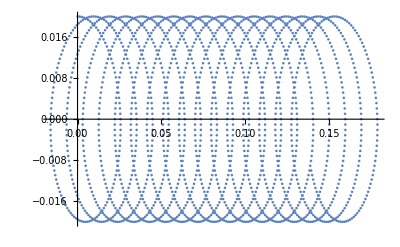

```mathematica
Clear["Global`*"]
NotebookEvaluate["/Users/tomoaki/Dropbox/code/cpp/mathematica_utilities/mathematica_plot_options.nb"]

(*name="student@10.0.1.9://home/student/BEM/Kramer2021_0d03/result.json"*)
(*data01DLPF4=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/LPF4/01D_LPF4.txt"}],"Data"];
data01DFNPF1=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/FNPF1/01D_FNPF1.txt"}],"Data"];
data01DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/01D_CI95_Normalized.txt"}],"Data"];
data03DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/03D_Measured1_Normalized.txt"}],"Data"];
data05DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/05D_Measured1_Normalized.txt"}],"Data"];
*)

(*ExperimentData=Import[NotebookDirectory[]<>"Ren2015_Fig14_H0d04_T1d2.csv"];
name="/Volumes/home/BEM/流体力学会2023/Ren2015_H0d04_T1d2_potential_2/result.json"*)

ExperimentData=Import[NotebookDirectory[]<>"Ren2015_Fig14_H0d1_T1d2.csv"];
ExperimentData0d04=Import[NotebookDirectory[]<>"Ren2015_Fig14_H0d04_T1d2.csv"];
ExperimentData0d04Heave=Import[NotebookDirectory[]<>"Ren2015_Fig11_H0d04_T1d2_heave.csv"];
ExperimentData0d04Surge=Import[NotebookDirectory[]<>"Ren2015_Fig11_H0d04_T1d2_surge.csv"];
ExperimentData0d04Pitch=Import[NotebookDirectory[]<>"Ren2015_Fig11_H0d04_T1d2_pitch.csv"];
name="/Volumes/home/BEM/20230922流体力学会年会東京農業大学/Ren2015_H0d04_T1d2_potential_2/result.json"
(*name="/Users/tomoaki/BEM/Cheng2018meshC_H0d04_T1d2_piston_with_float_ALE1/result.json";*)
name="/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_piston_with_float_ALE1/result.json";
(*name="/Users/tomoaki/BEM/Li_Cheng2018meshB_H0d04_T1d2_piston_positive/result.json"*)
(*name="/Users/tomoaki/BEM/Li_Cheng2018_H0d04_T1d2_flap/result.json"*)
(*name="/Users/tomoaki/BEM/Li_Cheng2018_H0d04_T1d2_potential/result.json"*)
(*name="/Users/tomoaki/BEM/Li_Cheng2018_H0d04_T1d2_potential_pahse_shift/result.json"*)
(*name="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_piston_2_positive_start_long/result.json"*)
(*name="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_piston_2_negative_start_long/result.json"*)
(*name="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_potential_2/result.json"*)

imported=Import[name];
getData[var_,n_:0]:=If[n>0,(var/.imported)[[;;,n]],var/.imported];
importGetData[name_,var_,n_:0]:=With[{imported=Import[name]},If[n>0,(var/.imported)[[;;,n]],var/.imported]];
importData[name_,var_,n_:0]:=With[{imported=Import[name]},If[n>0,(var/.imported)[[;;,n]],var/.imported]];
(*Kramer20210d03=Import[NotebookDirectory[]<>"Kramer2021_0d3.csv"];*)
jsonInfo[name_]:=With[{imported=Import[name,"JSON"]},Grid[Join[{{"no.","title","length"}},Table[{i,imported[[i]][[1]],Length[imported[[i]][[2]]]},{i,1,Min[10,Length[imported]]}]],Frame->All,Background->{None,{LightGray,{LightGreen,Green}}}]]
jsonInfo[name]
legend=LineLegend[{"mesh A","mesh B","mesh C","mesh D","mesh E","Exp (Ren et al., 2015)"},LegendMarkerSize->20,LabelStyle->10];
plotstyle={{Red,Dashed},{Blue},{Green,Dashed},{Orange},{Magenta},{Black}};
h=0.4;
d=0.1;
H=0.04;
T=1.2;

w=2π/T;
g=9.81;
Clear[k];
NSolve[w^2==g*k*Tanh[h*k],k,Reals];
k=Abs[k/.%[[1]]]
shift=5.7;

λ=2π*k;
c=Sqrt[g*λ/(2π)*Tanh[2π*h/λ]]
ρ=1000;
a=H/2;
stokesdrift[t_,x_,z_]:={a*w*Cosh[k(z+h)]/Sinh[k*h] Cos[w*t-k*x]+1/2*w*k*a*a*(Cosh[2*k(z+h)]-Cos[2(w*t-k*x)])/Sinh[k*h]^2,-a*w Sinh[k(z+h)]/Sinh[k*h] Sin[w*t-k*x]}
drift=Integrate[stokesdrift[t,0,0],t];
ListPlot[Table[drift,{t,0,20,0.01}],PlotRange->All]
```

## ALEが計算結果に与える影響

```mathematica
(*メッシュが細かくなるに従って，計算結果が収束することを期待していた．しかし，波の運動は早く収束するのだが，浮体の運動は直線的に収束しているようには見えなかった．
浮体周辺のメッシュの細かさが影響するだろうと考え計算したところ，浮体の運動は確かに大きく変化したが，期待する収束方向に変化しなかった．
メッシュの細かさはALEによる修正度合いにも影響を与えるだろうから，これまで確認したメッシュと計算の関係は，実はALEと計算の関係が根本的には決めているのではないかと考えた．
そこで，ALEを適用する頻度N，N time_stepに1度，を変更して計算結果を比較してみる．

ALEはできるだけ少ない方が収束しやすい，のような結果が得られるのではないか．

結果：ALEの頻度は，結果に影響を及ぼさなかった．
慣性モーメントが正しくないためにこのような結果になったと考えられる．
*)
```

```mathematica
meshAALE1="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_piston/result.json";
meshAALE3="/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_piston_positive_ALE3/result.json";
meshAALE6="/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_piston_positive_ALE6/result.json";
ListPlot[
{{importGetData[meshAALE1,"simulation_time"],(importGetData[meshAALE1,"float_pitch"])}ᵀ,
{importGetData[meshAALE3,"simulation_time"],(importGetData[meshAALE3,"float_pitch"])}ᵀ,
{importGetData[meshAALE6,"simulation_time"],(importGetData[meshAALE6,"float_pitch"])}ᵀ,
{T*#1+shift,k*h#2}&@@@ExperimentData0d04Pitch},
Joined->{True,True,True,True,True},
PlotStyle->plotstyle,
(*PlotRange->{{0,2.},{-1.,1.}},*)
PlotRange->{All,Automatic},
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["pitch",FontSize->20,FontFamily->"Times"]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
]
```

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_piston_positive_ALE3/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_piston_positive_ALE3/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Transpose::nmtx: {simulation_time/.$Failed,float_pitch/.$Failed}の最初の2個のレベルは転置できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_piston_positive_ALE6/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Transpose::nmtx: {simulation_time/.$Failed,float_pitch/.$Failed}の最初の2個のレベルは転置できません．

ListPlot::lpn: {{{0.00001,-3.15027×10^-9}},{},{},{}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{{{1/100000,-3.15027×10^-9}},Transpose[{simulation_time/.$Failed,float_pitch/.$Failed}],Transpose[{simulation_time/.$Failed,float_pitch/.$Failed}],$Failed},Joined→{True,True,True,True,True},PlotStyle→{{RGBColor[1, 0, 0],Dashing[{Small,Small}]},{RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],Dashing[{Small,Small}]},{RGBColor[1, 0.5, 0]},{RGBColor[1, 0, 1]},{GrayLevel[0]}},PlotRange→{All,Automatic},GridLines→{{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.},{-1.,-0.5,0.,0.5,1.}},FrameLabel→{t/T,pitch},FrameStyle→Directive[FontSize→20,GrayLevel[0],Thickness[0.002]],GridLines→{{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.},{-1.,-0.5,0.,0.5,1.}},GridLinesStyle→Directive[GrayLevel[0.5],Dashing[{0,Small}]],PlotLegends→Placed[LineLegend[{mesh A,mesh B,mesh C,mesh D,mesh E,Exp (Ren et al., 2015)},LegendMarkerSize→20,LabelStyle→10],{0.65,0.15}],{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

## メッシュの細かさが計算結果に与える影響

```mathematica
opt={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->400,
PlotStyle->{{Blue},{Black},{Red}},
AspectRatio->1/3};
plotxrange={1,13};
(*メッシュと計算の収束*)

(*meshC="/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_piston_with_float_ALE1/result.json"*)
meshC="/Users/tomoaki/BEM/Cheng2018_H0d04_T1d2_piston_with_float_ALE1/result.json"
meshD=meshC;"/Users/tomoaki/BEM/Cheng2018meshD_H0d04_T1d2_piston_with_float_ALE1_saved/result.json"
Dimensions["cpu_time"/.Import[meshC]]
Dimensions["cpu_time"/.Import[meshD]]
```

/Users/tomoaki/BEM/Cheng2018_H0d04_T1d2_piston_with_float_ALE1/result.json

/Users/tomoaki/BEM/Cheng2018meshD_H0d04_T1d2_piston_with_float_ALE1_saved/result.json

{600}

{600}

```mathematica
Manipulate[
ListPlot[
{{importGetData[meshC,"float_COM",1],importGetData[meshC,"float_COM",3]-0.4}ᵀ,
{importGetData[meshD,"float_COM",1],importGetData[meshD,"float_COM",3]-0.4}ᵀ,
Table[drift,{t,0,10,0.01}],
(*{importGetData[meshC,"float_COM",1]-shift,importGetData[meshC,"float_COM",3]-0.4}ᵀ,
{importGetData[meshD,"float_COM",1]-shift,importGetData[meshD,"float_COM",3]-0.4}ᵀ,
{importGetData[meshE,"float_COM",1]-shift,importGetData[meshE,"float_COM",3]-0.4}ᵀ,*)
{#1,#2}&@@@ExperimentData0d04},
PlotRange->{{-0.04,0.04},All},
Joined->{True,True,True,True,True,True},
PlotStyle->plotstyle,
PlotRange->{Automatic,Automatic},
PlotLabel->shift,
FrameLabel->{Style["x",FontSize->20,FontFamily->"Times",Italic],Style["y",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->legend,
Evaluate[plot2Doption]
],{shift,3.3882,3.5}]
```

ListPlot::lpn: «1»は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

```mathematica
fig=ListPlot[
{{(importGetData[meshC,"simulation_time"]),(importGetData[meshC,"float_COM",3]-0.4)}ᵀ,
{(importGetData[meshD,"simulation_time"]),(importGetData[meshD,"float_COM",3]-0.4)}ᵀ,
{T*#1+shift,h#2}&@@@ExperimentData0d04Heave},
Evaluate[opt],
Joined->{True,True,True,True,True,True},
PlotStyle->plotstyle,
PlotRange->{{0,12.},{-0.07,0.07}},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z/H_0",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->legend,
Evaluate[plot2Doption]
]
```

ListPlot::lpn: {{{0.00001,0.},{0.00002,0.},{0.00003,0.},{0.00004,0.},{0.00005,0.},{0.00006,0.},{0.00007,0.},{0.00008,0.},{0.00009,0.},{0.0001,0.},{0.00011,0.},{0.05011,0.},{0.10011,0.},«25»,{1.12853,0.000251},{1.16907,0.000317},{1.18898,0.000355},{1.23042,0.000445},{1.25644,0.000511},{1.30142,0.000643},{1.32996,0.000741},{1.37573,0.000922},{1.39418,0.001005},{1.43844,0.001225},{1.45516,0.001318},{1.49861,0.001582},«550»},{«1»},{}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{{{1/100000,0.},{1/50000,0.},{3/100000,0.},{1/25000,0.},{1/20000,0.},{3/50000,0.},{7/100000,0.},{1/12500,0.},{9/100000,0.},{0.0001,0.},{0.00011,0.},{0.05011,0.},{0.10011,0.},{0.15011,0.},{0.20011,0.},{0.25011,0.},{0.30011,0.},{0.35011,0.},{0.40011,0.},{0.45011,1.×10^-6},{0.50011,1.×10^-6},{0.55011,2.×10^-6},{0.583206,3.×10^-6},{0.633206,6.×10^-6},{0.679492,9.×10^-6},{0.691452,0.00001},{0.739466,0.000015},{0.765708,0.000019},{0.814112,0.000029},{0.844568,0.000037},{0.894568,0.000054},{0.914457,0.000062},{0.964457,0.000088},{0.972725,0.000094},{1.00439,0.000116},{1.04677,0.000152},{1.06337,0.000169},{1.10611,0.00022},{1.12853,0.000251},{1.16907,0.000317},{1.18898,0.000355},{1.23042,0.000445},{1.25644,0.000511},{1.30142,0.000643},{1.32996,0.000741},{1.37573,0.000922},{1.39418,0.001005},{1.43844,0.001225},{1.45516,0.001318},{1.49861,0.001582},{1.5308,0.001802},{1.56964,0.002094},{1.59823,0.002329},{1.64268,0.002725},{1.68741,0.003162},{1.71283,0.003426},{1.75697,0.003908},{1.77807,0.004146},{1.82268,0.004665},{1.83996,0.004868},{1.88325,0.005379},{1.90202,0.005599},{1.94362,0.006072},{1.97998,0.006462},{2.00442,0.006706},{2.04425,0.007062},{2.08417,0.007354},{2.12394,0.007563},{2.15944,0.007667},{2.19866,0.007679},{2.23701,0.007573},{2.27587,0.007335},{2.31444,0.006959},{2.35293,0.006439},{2.39203,0.005759},{2.43214,0.004904},{2.47382,0.003853},{2.51661,0.002616},{2.55962,0.001232},{2.59527,-1.×10^-6},{2.6264,-0.001123},{2.65464,-0.002166},{2.68091,-0.003144},{2.70579,-0.004066},{2.72968,-0.004939},{2.75288,-0.005767},{2.77566,-0.00655},{2.79822,-0.007288},{2.8208,-0.007982},{2.84359,-0.008628},{2.86686,-0.009221},{2.89091,-0.009754},{2.91614,-0.010216},{2.94313,-0.010587},{2.97219,-0.010831},{3.00241,-0.010899},{3.03257,-0.010766},{3.06231,-0.010428},{3.0919,-0.009883},{3.1215,-0.009127},{3.15119,-0.008158},{3.1811,-0.006975},{3.21139,-0.005578},{3.23737,-0.004234},{3.25927,-0.003005},{3.27865,-0.001856},{3.29627,-0.000766},{3.31259,0.000275},{3.32792,0.001276},{3.34245,0.00224},{3.35636,0.003172},{3.36974,0.004074},{3.38268,0.004948},{3.39528,0.005796},{3.40757,0.006618},{3.41962,0.007415},{3.43148,0.008187},{3.44318,0.008936},{3.45475,0.00966},{3.46625,0.01036},{3.47769,0.011035},{3.48912,0.011684},{3.50056,0.012308},{3.51205,0.012905},{3.52364,0.013473},{3.53535,0.014012},{3.54724,0.014518},{3.55936,0.01499},{3.57177,0.015424},{3.58456,0.015815},{3.59781,0.016159},{3.61166,0.016447},{3.62629,0.016669},{3.64195,0.016809},{3.65869,0.016843},{3.67508,0.016757},{3.6909,0.016561},{3.70637,0.016258},{3.72169,0.01585},{3.73701,0.015334},{3.7525,0.014704},{3.76831,0.013949},{3.7846,0.013056},{3.80099,0.012044},{3.8175,0.010912},{3.83419,0.009662},{3.85105,0.008296},{3.86687,0.006929},{3.88072,0.00567},{3.89324,0.004488},{3.90478,0.003364},{3.91559,0.002287},{3.92581,0.001249},{3.93555,0.000244},{3.94489,-0.000732},{3.95391,-0.001681},{3.96265,-0.002607},{3.97115,-0.003512},{3.97946,-0.004396},{3.98759,-0.005262},{3.99557,-0.00611},{4.00343,-0.006942},{4.01118,-0.007757},{4.01885,-0.008558},{4.02644,-0.009343},{4.03398,-0.010113},{4.04147,-0.01087},{4.04894,-0.011612},{4.05639,-0.01234},{4.06383,-0.013053},{4.07129,-0.013753},{4.07876,-0.014438},{4.08627,-0.015108},{4.09384,-0.015764},{4.10146,-0.016404},{4.10916,-0.017028},{4.11696,-0.017635},{4.12487,-0.018225},{4.13292,-0.018796},{4.14113,-0.019347},{4.14953,-0.019876},{4.15815,-0.020382},{4.16702,-0.020862},{4.1762,-0.021314},{4.18575,-0.021732},{4.19573,-0.022113},{4.20626,-0.02245},{4.21745,-0.022733},{4.2295,-0.022949},{4.2427,-0.023077},{4.25749,-0.023085},{4.2735,-0.022929},{4.29013,-0.022584},{4.30674,-0.022054},{4.32296,-0.021359},{4.33872,-0.020518},{4.35361,-0.019577},{4.36785,-0.01855},{4.38157,-0.017446},{4.3949,-0.01627},{4.40792,-0.015028},{4.42073,-0.013724},{4.43338,-0.012359},{4.44593,-0.010935},{4.45803,-0.009504},{4.46915,-0.008141},{4.47954,-0.006833},{4.48935,-0.005569},{4.49869,-0.004344},{4.50765,-0.003153},{4.51628,-0.001992},{4.52463,-0.000857},{4.53275,0.000252},{4.54066,0.001338},{4.54839,0.002402},{4.55597,0.003445},{4.56342,0.004468},{4.57075,0.005473},{4.57798,0.006458},{4.58512,0.007426},{4.59218,0.008376},{4.59918,0.009309},{4.60613,0.010224},{4.61304,0.011122},{4.61991,0.012004},{4.62676,0.012868},{4.63359,0.013716},{4.64041,0.014546},{4.64724,0.015359},{4.65408,0.016154},{4.66095,0.016931},{4.66784,0.01769},{4.67477,0.01843},{4.68175,0.019151},{4.68879,0.019852},{4.69591,0.020532},{4.70312,0.02119},{4.71042,0.021825},{4.71785,0.022437},{4.72541,0.023022},{4.73313,0.023581},{4.74104,0.02411},{4.74917,0.024607},{4.75755,0.025069},{4.76623,0.025492},{4.77527,0.025872},{4.78475,0.0262},{4.79472,0.026469},{4.80465,0.026655},{4.81453,0.026761},{4.82439,0.026786},{4.83424,0.026729},{4.84409,0.026592},{4.85394,0.026373},{4.86381,0.026072},{4.87369,0.025691},{4.88359,0.025228},{4.8935,0.024686},{4.90344,0.024064},{4.91341,0.023363},{4.9234,0.022585},{4.93343,0.021731},{4.94349,0.020803},{4.95358,0.019802},{4.96372,0.018732},{4.9739,0.017593},{4.98413,0.016389},{4.99442,0.015123},{5.00477,0.013796},{5.0142,0.012544},{5.02281,0.01137},{5.0308,0.010256},{5.03831,0.00919},{5.04543,0.008163},{5.05226,0.007167},{5.05884,0.006197},{5.06522,0.005248},{5.07143,0.004318},{5.0775,0.003403},{5.08347,0.002502},{5.0893,0.001618},{5.0951,0.000737},{5.10081,-0.000129},{5.10647,-0.000989},{5.1121,-0.001841},{5.11764,-0.002678},{5.12311,-0.003502},{5.12853,-0.004313},{5.13388,-0.00511},{5.13919,-0.005896},{5.14447,-0.006671},{5.14972,-0.007436},{5.15496,-0.008193},{5.1602,-0.008941},{5.16544,-0.009681},{5.1707,-0.010414},{5.17597,-0.011139},{5.18129,-0.011861},{5.18665,-0.012576},{5.19206,-0.013285},{5.19752,-0.013989},{5.20305,-0.014686},{5.20866,-0.015379},{5.21436,-0.016066},{5.22016,-0.016747},{5.22608,-0.017424},{5.23216,-0.018097},{5.2384,-0.018767},{5.24484,-0.019432},{5.25151,-0.020093},{5.25843,-0.020749},{5.26566,-0.021399},{5.27323,-0.022042},{5.28113,-0.022669},{5.28929,-0.023269},{5.29775,-0.02384},{5.30656,-0.024376},{5.31578,-0.024873},{5.3255,-0.025326},{5.33582,-0.025725},{5.3469,-0.026058},{5.35896,-0.026308},{5.37232,-0.026449},{5.38572,-0.026446},{5.39911,-0.026299},{5.41254,-0.026011},{5.42597,-0.025584},{5.43918,-0.025032},{5.45212,-0.024369},{5.46465,-0.023615},{5.47655,-0.022801},{5.48794,-0.021937},{5.49894,-0.021029},{5.50962,-0.02008},{5.52004,-0.019095},{5.53026,-0.018077},{5.54031,-0.017026},{5.55024,-0.015945},{5.56008,-0.014835},{5.56986,-0.013697},{5.57962,-0.012531},{5.58938,-0.011338},{5.59917,-0.010117},{5.60902,-0.008869},{5.61896,-0.007592},{5.62902,-0.006286},{5.63924,-0.00495},{5.64966,-0.003583},{5.66033,-0.002182},{5.6713,-0.000745},{5.68257,0.000722},{5.69369,0.002155},{5.7047,0.003555},{5.71564,0.004924},{5.72656,0.006263},{5.73748,0.007571},{5.74845,0.008848},{5.75948,0.010093},{5.77063,0.011307},{5.78193,0.012487},{5.7934,0.013631},{5.80472,0.014702},{5.81569,0.015684},{5.8264,0.016585},{5.83689,0.017412},{5.84722,0.01817},{5.85741,0.018862},{5.86752,0.019491},{5.87757,0.020061},{5.88755,0.02057},{5.89744,0.021017},{5.90724,0.021405},{5.91698,0.021734},{5.92668,0.022007},{5.93634,0.022223},{5.94599,0.022385},{5.95564,0.022493},{5.96529,0.022546},{5.97498,0.022546},{5.98469,0.022492},{5.99445,0.022384},{6.00426,0.022223},{6.01413,0.022008},{6.02406,0.021739},{6.03404,0.021417},{6.04408,0.021042},{6.05418,0.020614},{6.06433,0.020135},{6.07455,0.019605},{6.08483,0.019025},{6.09518,0.018396},{6.1056,0.017718},{6.1161,0.016993},{6.12669,0.01622},{6.13739,0.0154},{6.1482,0.014534},{6.15914,0.013622},{6.17019,0.012666},{6.18016,0.011778},{6.18941,0.010933},{6.19793,0.010138},{6.20602,0.00937},{6.21362,0.00864},{6.22087,0.007933},{6.22784,0.007247},{6.23457,0.006578},{6.24112,0.005923},{6.24749,0.005281},{6.25373,0.004649},{6.25985,0.004027},{6.26588,0.003413},{6.27181,0.002805},{6.27768,0.002204},{6.28349,0.001609},{6.28925,0.001018},{6.29497,0.000431},{6.30067,-0.000152},{6.30633,-0.000731},{6.31199,-0.001308},{6.31763,-0.001881},{6.32327,-0.002453},{6.32892,-0.003023},{6.33459,-0.003591},{6.34027,-0.004157},{6.34599,-0.004723},{6.35174,-0.005289},{6.35754,-0.005854},{6.3634,-0.00642},{6.36931,-0.006986},{6.3753,-0.007552},{6.38138,-0.00812},{6.38754,-0.008688},{6.3938,-0.009258},{6.40019,-0.009829},{6.40669,-0.010401},{6.41333,-0.010975},{6.42013,-0.01155},{6.4271,-0.012126},{6.43425,-0.012703},{6.44161,-0.01328},{6.44919,-0.013858},{6.45704,-0.014436},{6.46518,-0.015014},{6.47365,-0.015589},{6.48248,-0.016162},{6.49173,-0.01673},{6.50144,-0.017289},{6.51167,-0.017837},{6.52249,-0.018368},{6.53398,-0.018876},{6.54618,-0.019349},{6.5589,-0.019769},{6.57202,-0.02012},{6.58509,-0.020385},{6.59812,-0.020564},{6.61113,-0.020656},{6.62413,-0.020659},{6.63715,-0.020573},{6.65021,-0.020397},{6.66334,-0.02013},{6.67655,-0.019768},{6.68967,-0.019318},{6.7026,-0.018788},{6.71539,-0.018179},{6.72808,-0.017494},{6.74073,-0.016733},{6.75336,-0.015898},{6.76602,-0.014988},{6.77874,-0.014003},{6.79157,-0.012942},{6.80455,-0.011805},{6.81771,-0.010588},{6.83111,-0.009291},{6.84478,-0.007912},{6.85878,-0.006448},{6.8722,-0.005002},{6.88475,-0.003619},{6.89662,-0.002288},{6.90795,-0.001002},{6.91884,0.000244},{6.92937,0.001454},{6.93959,0.002632},{6.94957,0.003779},{6.95933,0.004897},{6.96892,0.005988},{6.97836,0.007053},{6.98769,0.008093},{6.99693,0.009108},{7.00611,0.0101},{7.01523,0.011067},{7.02434,0.012011},{7.03344,0.01293},{7.04255,0.013826},{7.05171,0.014698},{7.06092,0.015545},{7.07022,0.016366},{7.07963,0.017161},{7.08918,0.017928},{7.0989,0.018666},{7.10884,0.019373},{7.11902,0.020047},{7.12952,0.020684},{7.14039,0.021281},{7.15151,0.021824},{7.16262,0.022293},{7.17373,0.02269},{7.18488,0.023012},{7.19611,0.023259},{7.20744,0.023428},{7.21893,0.023515},{7.23043,0.023519},{7.24196,0.023437},{7.25351,0.023269},{7.2651,0.023016},{7.27675,0.022675},{7.28848,0.022247},{7.30031,0.021729},{7.31225,0.021122},{7.32434,0.020423},{7.33657,0.019631},{7.34898,0.018746},{7.36159,0.017765},{7.3744,0.01669},{7.38742,0.015519},{7.39863,0.014455},{7.40828,0.013499},{7.41686,0.01262},{7.42468,0.011799},{7.4319,0.011022},{7.43868,0.01028},{7.4451,0.009566},{7.45123,0.008874},{7.45712,0.008202},{7.46281,0.007545},{7.46834,0.006902},{7.47372,0.006271},{7.47897,0.00565},{7.48412,0.005039},{7.48917,0.004435},{7.49412,0.003843},{7.49903,0.003252},{7.50385,0.002671},{7.50863,0.002094},{7.51337,0.001521},{7.51808,0.000951},{7.52277,0.000384},{7.52744,-0.00018},{7.53211,-0.000743},{7.53677,-0.001303},{7.54143,-0.001863},{7.5461,-0.002421},{7.55078,-0.002979},{7.55548,-0.003536},{7.5602,-0.004094},{7.56495,-0.004651},{7.56974,-0.005209},{7.57457,-0.005767},{7.57944,-0.006325},{7.58437,-0.006884},{7.58935,-0.007445},{7.5944,-0.008006},{7.59953,-0.00857},{7.60474,-0.009135},{7.61003,-0.009701},{7.61543,-0.010269},{7.62094,-0.010841},{7.62656,-0.011412},{7.63232,-0.011986},{7.63821,-0.01256},{7.64425,-0.013136},{7.65047,-0.013713},{7.65686,-0.014289},{7.66346,-0.014866},{7.6703,-0.015443},{7.67739,-0.016019},{7.68479,-0.016594},{7.69252,-0.017167},{7.70064,-0.017736},{7.70921,-0.018299},{7.71801,-0.018837},{7.72709,-0.019347},{7.73649,-0.019827},{7.74626,-0.020273},{7.75648,-0.020679},{7.76723,-0.02104},{7.77862,-0.021347},{7.7908,-0.021589},{7.80324,-0.021742},{7.8157,-0.021801},{7.82821,-0.021764},{7.84076,-0.021631},{7.85338,-0.021401},{7.86605,-0.021074},{7.8787,-0.020654},{7.89116,-0.02015},{7.90347,-0.019566},{7.91568,-0.018905},{7.92785,-0.018169},{7.94,-0.017357},{7.95212,-0.016477}},{{1/100000,0.},{1/50000,0.},{3/100000,0.},{1/25000,0.},{1/20000,0.},{3/50000,0.},{7/100000,0.},{1/12500,0.},{9/100000,0.},{0.0001,0.},{0.00011,0.},{0.05011,0.},{0.10011,0.},{0.15011,0.},{0.20011,0.},{0.25011,0.},{0.30011,0.},{0.35011,0.},{0.40011,0.},{0.45011,1.×10^-6},{0.50011,1.×10^-6},{0.55011,2.×10^-6},{0.583206,3.×10^-6},{0.633206,6.×10^-6},{0.679492,9.×10^-6},{0.691452,0.00001},{0.739466,0.000015},{0.765708,0.000019},{0.814112,0.000029},{0.844568,0.000037},{0.894568,0.000054},{0.914457,0.000062},{0.964457,0.000088},{0.972725,0.000094},{1.00439,0.000116},{1.04677,0.000152},{1.06337,0.000169},{1.10611,0.00022},{1.12853,0.000251},{1.16907,0.000317},{1.18898,0.000355},{1.23042,0.000445},{1.25644,0.000511},{1.30142,0.000643},{1.32996,0.000741},{1.37573,0.000922},{1.39418,0.001005},{1.43844,0.001225},{1.45516,0.001318},{1.49861,0.001582},{1.5308,0.001802},{1.56964,0.002094},{1.59823,0.002329},{1.64268,0.002725},{1.68741,0.003162},{1.71283,0.003426},{1.75697,0.003908},{1.77807,0.004146},{1.82268,0.004665},{1.83996,0.004868},{1.88325,0.005379},{1.90202,0.005599},{1.94362,0.006072},{1.97998,0.006462},{2.00442,0.006706},{2.04425,0.007062},{2.08417,0.007354},{2.12394,0.007563},{2.15944,0.007667},{2.19866,0.007679},{2.23701,0.007573},{2.27587,0.007335},{2.31444,0.006959},{2.35293,0.006439},{2.39203,0.005759},{2.43214,0.004904},{2.47382,0.003853},{2.51661,0.002616},{2.55962,0.001232},{2.59527,-1.×10^-6},{2.6264,-0.001123},{2.65464,-0.002166},{2.68091,-0.003144},{2.70579,-0.004066},{2.72968,-0.004939},{2.75288,-0.005767},{2.77566,-0.00655},{2.79822,-0.007288},{2.8208,-0.007982},{2.84359,-0.008628},{2.86686,-0.009221},{2.89091,-0.009754},{2.91614,-0.010216},{2.94313,-0.010587},{2.97219,-0.010831},{3.00241,-0.010899},{3.03257,-0.010766},{3.06231,-0.010428},{3.0919,-0.009883},{3.1215,-0.009127},{3.15119,-0.008158},{3.1811,-0.006975},{3.21139,-0.005578},{3.23737,-0.004234},{3.25927,-0.003005},{3.27865,-0.001856},{3.29627,-0.000766},{3.31259,0.000275},{3.32792,0.001276},{3.34245,0.00224},{3.35636,0.003172},{3.36974,0.004074},{3.38268,0.004948},{3.39528,0.005796},{3.40757,0.006618},{3.41962,0.007415},{3.43148,0.008187},{3.44318,0.008936},{3.45475,0.00966},{3.46625,0.01036},{3.47769,0.011035},{3.48912,0.011684},{3.50056,0.012308},{3.51205,0.012905},{3.52364,0.013473},{3.53535,0.014012},{3.54724,0.014518},{3.55936,0.01499},{3.57177,0.015424},{3.58456,0.015815},{3.59781,0.016159},{3.61166,0.016447},{3.62629,0.016669},{3.64195,0.016809},{3.65869,0.016843},{3.67508,0.016757},{3.6909,0.016561},{3.70637,0.016258},{3.72169,0.01585},{3.73701,0.015334},{3.7525,0.014704},{3.76831,0.013949},{3.7846,0.013056},{3.80099,0.012044},{3.8175,0.010912},{3.83419,0.009662},{3.85105,0.008296},{3.86687,0.006929},{3.88072,0.00567},{3.89324,0.004488},{3.90478,0.003364},{3.91559,0.002287},{3.92581,0.001249},{3.93555,0.000244},{3.94489,-0.000732},{3.95391,-0.001681},{3.96265,-0.002607},{3.97115,-0.003512},{3.97946,-0.004396},{3.98759,-0.005262},{3.99557,-0.00611},{4.00343,-0.006942},{4.01118,-0.007757},{4.01885,-0.008558},{4.02644,-0.009343},{4.03398,-0.010113},{4.04147,-0.01087},{4.04894,-0.011612},{4.05639,-0.01234},{4.06383,-0.013053},{4.07129,-0.013753},{4.07876,-0.014438},{4.08627,-0.015108},{4.09384,-0.015764},{4.10146,-0.016404},{4.10916,-0.017028},{4.11696,-0.017635},{4.12487,-0.018225},{4.13292,-0.018796},{4.14113,-0.019347},{4.14953,-0.019876},{4.15815,-0.020382},{4.16702,-0.020862},{4.1762,-0.021314},{4.18575,-0.021732},{4.19573,-0.022113},{4.20626,-0.02245},{4.21745,-0.022733},{4.2295,-0.022949},{4.2427,-0.023077},{4.25749,-0.023085},{4.2735,-0.022929},{4.29013,-0.022584},{4.30674,-0.022054},{4.32296,-0.021359},{4.33872,-0.020518},{4.35361,-0.019577},{4.36785,-0.01855},{4.38157,-0.017446},{4.3949,-0.01627},{4.40792,-0.015028},{4.42073,-0.013724},{4.43338,-0.012359},{4.44593,-0.010935},{4.45803,-0.009504},{4.46915,-0.008141},{4.47954,-0.006833},{4.48935,-0.005569},{4.49869,-0.004344},{4.50765,-0.003153},{4.51628,-0.001992},{4.52463,-0.000857},{4.53275,0.000252},{4.54066,0.001338},{4.54839,0.002402},{4.55597,0.003445},{4.56342,0.004468},{4.57075,0.005473},{4.57798,0.006458},{4.58512,0.007426},{4.59218,0.008376},{4.59918,0.009309},{4.60613,0.010224},{4.61304,0.011122},{4.61991,0.012004},{4.62676,0.012868},{4.63359,0.013716},{4.64041,0.014546},{4.64724,0.015359},{4.65408,0.016154},{4.66095,0.016931},{4.66784,0.01769},{4.67477,0.01843},{4.68175,0.019151},{4.68879,0.019852},{4.69591,0.020532},{4.70312,0.02119},{4.71042,0.021825},{4.71785,0.022437},{4.72541,0.023022},{4.73313,0.023581},{4.74104,0.02411},{4.74917,0.024607},{4.75755,0.025069},{4.76623,0.025492},{4.77527,0.025872},{4.78475,0.0262},{4.79472,0.026469},{4.80465,0.026655},{4.81453,0.026761},{4.82439,0.026786},{4.83424,0.026729},{4.84409,0.026592},{4.85394,0.026373},{4.86381,0.026072},{4.87369,0.025691},{4.88359,0.025228},{4.8935,0.024686},{4.90344,0.024064},{4.91341,0.023363},{4.9234,0.022585},{4.93343,0.021731},{4.94349,0.020803},{4.95358,0.019802},{4.96372,0.018732},{4.9739,0.017593},{4.98413,0.016389},{4.99442,0.015123},{5.00477,0.013796},{5.0142,0.012544},{5.02281,0.01137},{5.0308,0.010256},{5.03831,0.00919},{5.04543,0.008163},{5.05226,0.007167},{5.05884,0.006197},{5.06522,0.005248},{5.07143,0.004318},{5.0775,0.003403},{5.08347,0.002502},{5.0893,0.001618},{5.0951,0.000737},{5.10081,-0.000129},{5.10647,-0.000989},{5.1121,-0.001841},{5.11764,-0.002678},{5.12311,-0.003502},{5.12853,-0.004313},{5.13388,-0.00511},{5.13919,-0.005896},{5.14447,-0.006671},{5.14972,-0.007436},{5.15496,-0.008193},{5.1602,-0.008941},{5.16544,-0.009681},{5.1707,-0.010414},{5.17597,-0.011139},{5.18129,-0.011861},{5.18665,-0.012576},{5.19206,-0.013285},{5.19752,-0.013989},{5.20305,-0.014686},{5.20866,-0.015379},{5.21436,-0.016066},{5.22016,-0.016747},{5.22608,-0.017424},{5.23216,-0.018097},{5.2384,-0.018767},{5.24484,-0.019432},{5.25151,-0.020093},{5.25843,-0.020749},{5.26566,-0.021399},{5.27323,-0.022042},{5.28113,-0.022669},{5.28929,-0.023269},{5.29775,-0.02384},{5.30656,-0.024376},{5.31578,-0.024873},{5.3255,-0.025326},{5.33582,-0.025725},{5.3469,-0.026058},{5.35896,-0.026308},{5.37232,-0.026449},{5.38572,-0.026446},{5.39911,-0.026299},{5.41254,-0.026011},{5.42597,-0.025584},{5.43918,-0.025032},{5.45212,-0.024369},{5.46465,-0.023615},{5.47655,-0.022801},{5.48794,-0.021937},{5.49894,-0.021029},{5.50962,-0.02008},{5.52004,-0.019095},{5.53026,-0.018077},{5.54031,-0.017026},{5.55024,-0.015945},{5.56008,-0.014835},{5.56986,-0.013697},{5.57962,-0.012531},{5.58938,-0.011338},{5.59917,-0.010117},{5.60902,-0.008869},{5.61896,-0.007592},{5.62902,-0.006286},{5.63924,-0.00495},{5.64966,-0.003583},{5.66033,-0.002182},{5.6713,-0.000745},{5.68257,0.000722},{5.69369,0.002155},{5.7047,0.003555},{5.71564,0.004924},{5.72656,0.006263},{5.73748,0.007571},{5.74845,0.008848},{5.75948,0.010093},{5.77063,0.011307},{5.78193,0.012487},{5.7934,0.013631},{5.80472,0.014702},{5.81569,0.015684},{5.8264,0.016585},{5.83689,0.017412},{5.84722,0.01817},{5.85741,0.018862},{5.86752,0.019491},{5.87757,0.020061},{5.88755,0.02057},{5.89744,0.021017},{5.90724,0.021405},{5.91698,0.021734},{5.92668,0.022007},{5.93634,0.022223},{5.94599,0.022385},{5.95564,0.022493},{5.96529,0.022546},{5.97498,0.022546},{5.98469,0.022492},{5.99445,0.022384},{6.00426,0.022223},{6.01413,0.022008},{6.02406,0.021739},{6.03404,0.021417},{6.04408,0.021042},{6.05418,0.020614},{6.06433,0.020135},{6.07455,0.019605},{6.08483,0.019025},{6.09518,0.018396},{6.1056,0.017718},{6.1161,0.016993},{6.12669,0.01622},{6.13739,0.0154},{6.1482,0.014534},{6.15914,0.013622},{6.17019,0.012666},{6.18016,0.011778},{6.18941,0.010933},{6.19793,0.010138},{6.20602,0.00937},{6.21362,0.00864},{6.22087,0.007933},{6.22784,0.007247},{6.23457,0.006578},{6.24112,0.005923},{6.24749,0.005281},{6.25373,0.004649},{6.25985,0.004027},{6.26588,0.003413},{6.27181,0.002805},{6.27768,0.002204},{6.28349,0.001609},{6.28925,0.001018},{6.29497,0.000431},{6.30067,-0.000152},{6.30633,-0.000731},{6.31199,-0.001308},{6.31763,-0.001881},{6.32327,-0.002453},{6.32892,-0.003023},{6.33459,-0.003591},{6.34027,-0.004157},{6.34599,-0.004723},{6.35174,-0.005289},{6.35754,-0.005854},{6.3634,-0.00642},{6.36931,-0.006986},{6.3753,-0.007552},{6.38138,-0.00812},{6.38754,-0.008688},{6.3938,-0.009258},{6.40019,-0.009829},{6.40669,-0.010401},{6.41333,-0.010975},{6.42013,-0.01155},{6.4271,-0.012126},{6.43425,-0.012703},{6.44161,-0.01328},{6.44919,-0.013858},{6.45704,-0.014436},{6.46518,-0.015014},{6.47365,-0.015589},{6.48248,-0.016162},{6.49173,-0.01673},{6.50144,-0.017289},{6.51167,-0.017837},{6.52249,-0.018368},{6.53398,-0.018876},{6.54618,-0.019349},{6.5589,-0.019769},{6.57202,-0.02012},{6.58509,-0.020385},{6.59812,-0.020564},{6.61113,-0.020656},{6.62413,-0.020659},{6.63715,-0.020573},{6.65021,-0.020397},{6.66334,-0.02013},{6.67655,-0.019768},{6.68967,-0.019318},{6.7026,-0.018788},{6.71539,-0.018179},{6.72808,-0.017494},{6.74073,-0.016733},{6.75336,-0.015898},{6.76602,-0.014988},{6.77874,-0.014003},{6.79157,-0.012942},{6.80455,-0.011805},{6.81771,-0.010588},{6.83111,-0.009291},{6.84478,-0.007912},{6.85878,-0.006448},{6.8722,-0.005002},{6.88475,-0.003619},{6.89662,-0.002288},{6.90795,-0.001002},{6.91884,0.000244},{6.92937,0.001454},{6.93959,0.002632},{6.94957,0.003779},{6.95933,0.004897},{6.96892,0.005988},{6.97836,0.007053},{6.98769,0.008093},{6.99693,0.009108},{7.00611,0.0101},{7.01523,0.011067},{7.02434,0.012011},{7.03344,0.01293},{7.04255,0.013826},{7.05171,0.014698},{7.06092,0.015545},{7.07022,0.016366},{7.07963,0.017161},{7.08918,0.017928},{7.0989,0.018666},{7.10884,0.019373},{7.11902,0.020047},{7.12952,0.020684},{7.14039,0.021281},{7.15151,0.021824},{7.16262,0.022293},{7.17373,0.02269},{7.18488,0.023012},{7.19611,0.023259},{7.20744,0.023428},{7.21893,0.023515},{7.23043,0.023519},{7.24196,0.023437},{7.25351,0.023269},{7.2651,0.023016},{7.27675,0.022675},{7.28848,0.022247},{7.30031,0.021729},{7.31225,0.021122},{7.32434,0.020423},{7.33657,0.019631},{7.34898,0.018746},{7.36159,0.017765},{7.3744,0.01669},{7.38742,0.015519},{7.39863,0.014455},{7.40828,0.013499},{7.41686,0.01262},{7.42468,0.011799},{7.4319,0.011022},{7.43868,0.01028},{7.4451,0.009566},{7.45123,0.008874},{7.45712,0.008202},{7.46281,0.007545},{7.46834,0.006902},{7.47372,0.006271},{7.47897,0.00565},{7.48412,0.005039},{7.48917,0.004435},{7.49412,0.003843},{7.49903,0.003252},{7.50385,0.002671},{7.50863,0.002094},{7.51337,0.001521},{7.51808,0.000951},{7.52277,0.000384},{7.52744,-0.00018},{7.53211,-0.000743},{7.53677,-0.001303},{7.54143,-0.001863},{7.5461,-0.002421},{7.55078,-0.002979},{7.55548,-0.003536},{7.5602,-0.004094},{7.56495,-0.004651},{7.56974,-0.005209},{7.57457,-0.005767},{7.57944,-0.006325},{7.58437,-0.006884},{7.58935,-0.007445},{7.5944,-0.008006},{7.59953,-0.00857},{7.60474,-0.009135},{7.61003,-0.009701},{7.61543,-0.010269},{7.62094,-0.010841},{7.62656,-0.011412},{7.63232,-0.011986},{7.63821,-0.01256},{7.64425,-0.013136},{7.65047,-0.013713},{7.65686,-0.014289},{7.66346,-0.014866},{7.6703,-0.015443},{7.67739,-0.016019},{7.68479,-0.016594},{7.69252,-0.017167},{7.70064,-0.017736},{7.70921,-0.018299},{7.71801,-0.018837},{7.72709,-0.019347},{7.73649,-0.019827},{7.74626,-0.020273},{7.75648,-0.020679},{7.76723,-0.02104},{7.77862,-0.021347},{7.7908,-0.021589},{7.80324,-0.021742},{7.8157,-0.021801},{7.82821,-0.021764},{7.84076,-0.021631},{7.85338,-0.021401},{7.86605,-0.021074},{7.8787,-0.020654},{7.89116,-0.02015},{7.90347,-0.019566},{7.91568,-0.018905},{7.92785,-0.018169},{7.94,-0.017357},{7.95212,-0.016477}},$Failed},{FrameStyle→Directive[FontSize→16,GrayLevel[0],Thickness[0.002]],GridLines→All,GridLinesStyle→Directive[GrayLevel[0.5],AbsoluteThickness[0.001]],ImageSize→400,PlotStyle→{{RGBColor[0, 0, 1]},{GrayLevel[0]},{RGBColor[1, 0, 0]}},AspectRatio→1/3},Joined→{True,True,True,True,True,True},PlotStyle→{{RGBColor[1, 0, 0],Dashing[{Small,Small}]},{RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],Dashing[{Small,Small}]},{RGBColor[1, 0.5, 0]},{RGBColor[1, 0, 1]},{GrayLevel[0]}},PlotRange→{{0,12.},{-0.07,0.07}},FrameLabel→{t/T,z/H_0},PlotLegends→LineLegend[{mesh A,mesh B,mesh C,mesh D,mesh E,Exp (Ren et al., 2015)},LegendMarkerSize→20,LabelStyle→10],{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

```mathematica
ListPlot[
{{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_COM",1]-3.375)}ᵀ,
{importGetData[meshD,"simulation_time"],(importGetData[meshD,"float_COM",1]-3.375)}ᵀ,
{T*#1+shift,h#2}&@@@ExperimentData0d04Surge},
Joined->{True,True,True,True,True,True},
Evaluate[opt],
PlotStyle->plotstyle,
PlotRange->{{0,12.},Automatic},
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->legend,
Evaluate[plot2Doption]
]
```

ListPlot::lpn: {{{0.00001,-0.025},{0.00002,-0.025},{0.00003,-0.025},{0.00004,-0.025},{0.00005,-0.025},{0.00006,-0.025},{0.00007,-0.025},{0.00008,-0.025},{0.00009,-0.025},{0.0001,-0.025},«32»,{1.25644,-0.02456},{1.30142,-0.02443},{1.32996,-0.02432},{1.37573,-0.02413},{1.39418,-0.02403},{1.43844,-0.02378},{1.45516,-0.02367},{1.49861,-0.02335},«550»},{«1»},{}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{{{1/100000,-0.025},{1/50000,-0.025},{3/100000,-0.025},{1/25000,-0.025},{1/20000,-0.025},{3/50000,-0.025},{7/100000,-0.025},{1/12500,-0.025},{9/100000,-0.025},{0.0001,-0.025},{0.00011,-0.025},{0.05011,-0.025},{0.10011,-0.025},{0.15011,-0.025},{0.20011,-0.025},{0.25011,-0.025},{0.30011,-0.025},{0.35011,-0.025},{0.40011,-0.025},{0.45011,-0.025},{0.50011,-0.025},{0.55011,-0.025},{0.583206,-0.025},{0.633206,-0.025},{0.679492,-0.02499},{0.691452,-0.02499},{0.739466,-0.02499},{0.765708,-0.02499},{0.814112,-0.02498},{0.844568,-0.02498},{0.894568,-0.02496},{0.914457,-0.02496},{0.964457,-0.02494},{0.972725,-0.02493},{1.00439,-0.02492},{1.04677,-0.02489},{1.06337,-0.02487},{1.10611,-0.02483},{1.12853,-0.0248},{1.16907,-0.02474},{1.18898,-0.02471},{1.23042,-0.02462},{1.25644,-0.02456},{1.30142,-0.02443},{1.32996,-0.02432},{1.37573,-0.02413},{1.39418,-0.02403},{1.43844,-0.02378},{1.45516,-0.02367},{1.49861,-0.02335},{1.5308,-0.02307},{1.56964,-0.02268},{1.59823,-0.02235},{1.64268,-0.02177},{1.68741,-0.0211},{1.71283,-0.02067},{1.75697,-0.01985},{1.77807,-0.01941},{1.82268,-0.01841},{1.83996,-0.018},{1.88325,-0.01688},{1.90202,-0.01636},{1.94362,-0.01513},{1.97998,-0.01399},{2.00442,-0.01319},{2.04425,-0.01183},{2.08417,-0.0104},{2.12394,-0.00894},{2.15944,-0.00762},{2.19866,-0.00616},{2.23701,-0.00475},{2.27587,-0.00337},{2.31444,-0.00207},{2.35293,-0.00086},{2.39203,0.00023},{2.43214,0.0012},{2.47382,0.00199},{2.51661,0.00257},{2.55962,0.00287},{2.59527,0.00289},{2.6264,0.00273},{2.65464,0.00244},{2.68091,0.00205},{2.70579,0.00157},{2.72968,0.00101},{2.75288,0.00038},{2.77566,-0.00032},{2.79822,-0.00109},{2.8208,-0.00194},{2.84359,-0.00285},{2.86686,-0.00385},{2.89091,-0.00493},{2.91614,-0.00611},{2.94313,-0.00742},{2.97219,-0.00885},{3.00241,-0.01033},{3.03257,-0.01179},{3.06231,-0.01316},{3.0919,-0.01445},{3.1215,-0.01561},{3.15119,-0.01663},{3.1811,-0.01747},{3.21139,-0.01812},{3.23737,-0.01847},{3.25927,-0.01863},{3.27865,-0.01864},{3.29627,-0.01856},{3.31259,-0.01839},{3.32792,-0.01815},{3.34245,-0.01785},{3.35636,-0.01751},{3.36974,-0.01711},{3.38268,-0.01667},{3.39528,-0.0162},{3.40757,-0.01568},{3.41962,-0.01513},{3.43148,-0.01455},{3.44318,-0.01393},{3.45475,-0.01329},{3.46625,-0.01261},{3.47769,-0.0119},{3.48912,-0.01116},{3.50056,-0.01039},{3.51205,-0.00959},{3.52364,-0.00875},{3.53535,-0.00788},{3.54724,-0.00697},{3.55936,-0.00603},{3.57177,-0.00505},{3.58456,-0.00402},{3.59781,-0.00294},{3.61166,-0.0018},{3.62629,-0.0006},{3.64195,0.00069},{3.65869,0.00205},{3.67508,0.00336},{3.6909,0.0046},{3.70637,0.00578},{3.72169,0.0069},{3.73701,0.00798},{3.7525,0.00901},{3.76831,0.01},{3.7846,0.01094},{3.80099,0.01181},{3.8175,0.01258},{3.83419,0.01327},{3.85105,0.01385},{3.86687,0.0143},{3.88072,0.0146},{3.89324,0.0148},{3.90478,0.01493},{3.91559,0.01499},{3.92581,0.01501},{3.93555,0.01498},{3.94489,0.01491},{3.95391,0.01481},{3.96265,0.01467},{3.97115,0.01451},{3.97946,0.01432},{3.98759,0.0141},{3.99557,0.01387},{4.00343,0.01361},{4.01118,0.01332},{4.01885,0.01302},{4.02644,0.0127},{4.03398,0.01235},{4.04147,0.01199},{4.04894,0.01161},{4.05639,0.0112},{4.06383,0.01078},{4.07129,0.01034},{4.07876,0.00988},{4.08627,0.0094},{4.09384,0.0089},{4.10146,0.00839},{4.10916,0.00784},{4.11696,0.00728},{4.12487,0.0067},{4.13292,0.00609},{4.14113,0.00545},{4.14953,0.00479},{4.15815,0.0041},{4.16702,0.00338},{4.1762,0.00262},{4.18575,0.00183},{4.19573,0.001},{4.20626,0.00011},{4.21745,-0.00083},{4.2295,-0.00184},{4.2427,-0.00293},{4.25749,-0.00414},{4.2735,-0.0054},{4.29013,-0.00667},{4.30674,-0.00787},{4.32296,-0.00897},{4.33872,-0.00995},{4.35361,-0.0108},{4.36785,-0.01153},{4.38157,-0.01214},{4.3949,-0.01266},{4.40792,-0.01308},{4.42073,-0.01341},{4.43338,-0.01366},{4.44593,-0.01381},{4.45803,-0.01387},{4.46915,-0.01385},{4.47954,-0.01377},{4.48935,-0.01364},{4.49869,-0.01346},{4.50765,-0.01324},{4.51628,-0.01298},{4.52463,-0.01268},{4.53275,-0.01236},{4.54066,-0.012},{4.54839,-0.01162},{4.55597,-0.01122},{4.56342,-0.01079},{4.57075,-0.01033},{4.57798,-0.00985},{4.58512,-0.00936},{4.59218,-0.00883},{4.59918,-0.00829},{4.60613,-0.00773},{4.61304,-0.00715},{4.61991,-0.00655},{4.62676,-0.00593},{4.63359,-0.00529},{4.64041,-0.00463},{4.64724,-0.00395},{4.65408,-0.00325},{4.66095,-0.00253},{4.66784,-0.00179},{4.67477,-0.00103},{4.68175,-0.00025},{4.68879,0.00055},{4.69591,0.00138},{4.70312,0.00222},{4.71042,0.0031},{4.71785,0.00399},{4.72541,0.00492},{4.73313,0.00587},{4.74104,0.00686},{4.74917,0.00788},{4.75755,0.00894},{4.76623,0.01004},{4.77527,0.01119},{4.78475,0.01239},{4.79472,0.01365},{4.80465,0.0149},{4.81453,0.01614},{4.82439,0.01736},{4.83424,0.01856},{4.84409,0.01975},{4.85394,0.02091},{4.86381,0.02205},{4.87369,0.02317},{4.88359,0.02426},{4.8935,0.02532},{4.90344,0.02635},{4.91341,0.02734},{4.9234,0.0283},{4.93343,0.02921},{4.94349,0.03009},{4.95358,0.03092},{4.96372,0.03171},{4.9739,0.03246},{4.98413,0.03315},{4.99442,0.03379},{5.00477,0.03438},{5.0142,0.03487},{5.02281,0.03527},{5.0308,0.0356},{5.03831,0.03589},{5.04543,0.03613},{5.05226,0.03633},{5.05884,0.0365},{5.06522,0.03665},{5.07143,0.03676},{5.0775,0.03686},{5.08347,0.03693},{5.0893,0.03698},{5.0951,0.03701},{5.10081,0.03703},{5.10647,0.03702},{5.1121,0.037},{5.11764,0.03696},{5.12311,0.03691},{5.12853,0.03684},{5.13388,0.03676},{5.13919,0.03666},{5.14447,0.03655},{5.14972,0.03642},{5.15496,0.03629},{5.1602,0.03614},{5.16544,0.03597},{5.1707,0.0358},{5.17597,0.03561},{5.18129,0.0354},{5.18665,0.03518},{5.19206,0.03495},{5.19752,0.0347},{5.20305,0.03444},{5.20866,0.03416},{5.21436,0.03386},{5.22016,0.03354},{5.22608,0.03321},{5.23216,0.03286},{5.2384,0.03248},{5.24484,0.03208},{5.25151,0.03165},{5.25843,0.03119},{5.26566,0.03069},{5.27323,0.03016},{5.28113,0.0296},{5.28929,0.029},{5.29775,0.02836},{5.30656,0.02769},{5.31578,0.02697},{5.3255,0.02621},{5.33582,0.02539},{5.3469,0.0245},{5.35896,0.02353},{5.37232,0.02246},{5.38572,0.02138},{5.39911,0.02033},{5.41254,0.01929},{5.42597,0.01827},{5.43918,0.0173},{5.45212,0.01638},{5.46465,0.01553},{5.47655,0.01476},{5.48794,0.01406},{5.49894,0.01341},{5.50962,0.01283},{5.52004,0.01229},{5.53026,0.01181},{5.54031,0.01136},{5.55024,0.01096},{5.56008,0.0106},{5.56986,0.01029},{5.57962,0.01001},{5.58938,0.00977},{5.59917,0.00957},{5.60902,0.00942},{5.61896,0.0093},{5.62902,0.00923},{5.63924,0.00921},{5.64966,0.00923},{5.66033,0.0093},{5.6713,0.00944},{5.68257,0.00963},{5.69369,0.00987},{5.7047,0.01017},{5.71564,0.01052},{5.72656,0.01093},{5.73748,0.01138},{5.74845,0.01189},{5.75948,0.01245},{5.77063,0.01307},{5.78193,0.01375},{5.7934,0.01449},{5.80472,0.01526},{5.81569,0.01606},{5.8264,0.01688},{5.83689,0.01772},{5.84722,0.01857},{5.85741,0.01945},{5.86752,0.02035},{5.87757,0.02127},{5.88755,0.02221},{5.89744,0.02316},{5.90724,0.02412},{5.91698,0.02509},{5.92668,0.02607},{5.93634,0.02707},{5.94599,0.02807},{5.95564,0.02908},{5.96529,0.0301},{5.97498,0.03113},{5.98469,0.03217},{5.99445,0.03321},{6.00426,0.03425},{6.01413,0.0353},{6.02406,0.03635},{6.03404,0.0374},{6.04408,0.03844},{6.05418,0.03947},{6.06433,0.0405},{6.07455,0.04151},{6.08483,0.04251},{6.09518,0.04349},{6.1056,0.04445},{6.1161,0.04539},{6.12669,0.0463},{6.13739,0.04719},{6.1482,0.04805},{6.15914,0.04888},{6.17019,0.04966},{6.18016,0.05033},{6.18941,0.05092},{6.19793,0.05143},{6.20602,0.05188},{6.21362,0.05228},{6.22087,0.05263},{6.22784,0.05295},{6.23457,0.05324},{6.24112,0.0535},{6.24749,0.05373},{6.25373,0.05393},{6.25985,0.05412},{6.26588,0.05428},{6.27181,0.05442},{6.27768,0.05455},{6.28349,0.05465},{6.28925,0.05474},{6.29497,0.05481},{6.30067,0.05487},{6.30633,0.0549},{6.31199,0.05492},{6.31763,0.05493},{6.32327,0.05492},{6.32892,0.05489},{6.33459,0.05485},{6.34027,0.05479},{6.34599,0.05471},{6.35174,0.05462},{6.35754,0.05451},{6.3634,0.05438},{6.36931,0.05423},{6.3753,0.05407},{6.38138,0.05388},{6.38754,0.05368},{6.3938,0.05345},{6.40019,0.05321},{6.40669,0.05293},{6.41333,0.05264},{6.42013,0.05232},{6.4271,0.05197},{6.43425,0.05159},{6.44161,0.05119},{6.44919,0.05074},{6.45704,0.05026},{6.46518,0.04975},{6.47365,0.04918},{6.48248,0.04857},{6.49173,0.04791},{6.50144,0.04719},{6.51167,0.04641},{6.52249,0.04556},{6.53398,0.04463},{6.54618,0.04363},{6.5589,0.04256},{6.57202,0.04143},{6.58509,0.04031},{6.59812,0.03918},{6.61113,0.03806},{6.62413,0.03695},{6.63715,0.03584},{6.65021,0.03476},{6.66334,0.0337},{6.67655,0.03266},{6.68967,0.03167},{6.7026,0.03073},{6.71539,0.02985},{6.72808,0.02903},{6.74073,0.02826},{6.75336,0.02755},{6.76602,0.02691},{6.77874,0.02632},{6.79157,0.0258},{6.80455,0.02535},{6.81771,0.02497},{6.83111,0.02467},{6.84478,0.02446},{6.85878,0.02433},{6.8722,0.02431},{6.88475,0.02437},{6.89662,0.0245},{6.90795,0.02469},{6.91884,0.02493},{6.92937,0.02523},{6.93959,0.02556},{6.94957,0.02594},{6.95933,0.02636},{6.96892,0.02682},{6.97836,0.0273},{6.98769,0.02783},{6.99693,0.02838},{7.00611,0.02897},{7.01523,0.02959},{7.02434,0.03024},{7.03344,0.03092},{7.04255,0.03164},{7.05171,0.03238},{7.06092,0.03316},{7.07022,0.03398},{7.07963,0.03482},{7.08918,0.03571},{7.0989,0.03664},{7.10884,0.0376},{7.11902,0.03862},{7.12952,0.03968},{7.14039,0.0408},{7.15151,0.04197},{7.16262,0.04314},{7.17373,0.04432},{7.18488,0.04551},{7.19611,0.04671},{7.20744,0.04792},{7.21893,0.04914},{7.23043,0.05036},{7.24196,0.05156},{7.25351,0.05275},{7.2651,0.05392},{7.27675,0.05506},{7.28848,0.05619},{7.30031,0.0573},{7.31225,0.05837},{7.32434,0.05942},{7.33657,0.06043},{7.34898,0.0614},{7.36159,0.06233},{7.3744,0.06322},{7.38742,0.06405},{7.39863,0.0647},{7.40828,0.06522},{7.41686,0.06565},{7.42468,0.06601},{7.4319,0.06632},{7.43868,0.06659},{7.4451,0.06682},{7.45123,0.06702},{7.45712,0.0672},{7.46281,0.06736},{7.46834,0.0675},{7.47372,0.06761},{7.47897,0.06772},{7.48412,0.0678},{7.48917,0.06787},{7.49412,0.06793},{7.49903,0.06798},{7.50385,0.06801},{7.50863,0.06803},{7.51337,0.06805},{7.51808,0.06805},{7.52277,0.06803},{7.52744,0.06801},{7.53211,0.06798},{7.53677,0.06794},{7.54143,0.06788},{7.5461,0.06782},{7.55078,0.06774},{7.55548,0.06766},{7.5602,0.06756},{7.56495,0.06746},{7.56974,0.06734},{7.57457,0.06721},{7.57944,0.06707},{7.58437,0.06691},{7.58935,0.06675},{7.5944,0.06657},{7.59953,0.06637},{7.60474,0.06616},{7.61003,0.06594},{7.61543,0.0657},{7.62094,0.06545},{7.62656,0.06517},{7.63232,0.06488},{7.63821,0.06457},{7.64425,0.06424},{7.65047,0.06388},{7.65686,0.0635},{7.66346,0.06309},{7.6703,0.06266},{7.67739,0.06219},{7.68479,0.06169},{7.69252,0.06115},{7.70064,0.06057},{7.70921,0.05994},{7.71801,0.05927},{7.72709,0.05857},{7.73649,0.05782},{7.74626,0.05704},{7.75648,0.0562},{7.76723,0.0553},{7.77862,0.05435},{7.7908,0.05332},{7.80324,0.05226},{7.8157,0.0512},{7.82821,0.05014},{7.84076,0.04909},{7.85338,0.04806},{7.86605,0.04703},{7.8787,0.04604},{7.89116,0.04509},{7.90347,0.04418},{7.91568,0.04332},{7.92785,0.0425},{7.94,0.04173},{7.95212,0.04101}},{{1/100000,-0.025},{1/50000,-0.025},{3/100000,-0.025},{1/25000,-0.025},{1/20000,-0.025},{3/50000,-0.025},{7/100000,-0.025},{1/12500,-0.025},{9/100000,-0.025},{0.0001,-0.025},{0.00011,-0.025},{0.05011,-0.025},{0.10011,-0.025},{0.15011,-0.025},{0.20011,-0.025},{0.25011,-0.025},{0.30011,-0.025},{0.35011,-0.025},{0.40011,-0.025},{0.45011,-0.025},{0.50011,-0.025},{0.55011,-0.025},{0.583206,-0.025},{0.633206,-0.025},{0.679492,-0.02499},{0.691452,-0.02499},{0.739466,-0.02499},{0.765708,-0.02499},{0.814112,-0.02498},{0.844568,-0.02498},{0.894568,-0.02496},{0.914457,-0.02496},{0.964457,-0.02494},{0.972725,-0.02493},{1.00439,-0.02492},{1.04677,-0.02489},{1.06337,-0.02487},{1.10611,-0.02483},{1.12853,-0.0248},{1.16907,-0.02474},{1.18898,-0.02471},{1.23042,-0.02462},{1.25644,-0.02456},{1.30142,-0.02443},{1.32996,-0.02432},{1.37573,-0.02413},{1.39418,-0.02403},{1.43844,-0.02378},{1.45516,-0.02367},{1.49861,-0.02335},{1.5308,-0.02307},{1.56964,-0.02268},{1.59823,-0.02235},{1.64268,-0.02177},{1.68741,-0.0211},{1.71283,-0.02067},{1.75697,-0.01985},{1.77807,-0.01941},{1.82268,-0.01841},{1.83996,-0.018},{1.88325,-0.01688},{1.90202,-0.01636},{1.94362,-0.01513},{1.97998,-0.01399},{2.00442,-0.01319},{2.04425,-0.01183},{2.08417,-0.0104},{2.12394,-0.00894},{2.15944,-0.00762},{2.19866,-0.00616},{2.23701,-0.00475},{2.27587,-0.00337},{2.31444,-0.00207},{2.35293,-0.00086},{2.39203,0.00023},{2.43214,0.0012},{2.47382,0.00199},{2.51661,0.00257},{2.55962,0.00287},{2.59527,0.00289},{2.6264,0.00273},{2.65464,0.00244},{2.68091,0.00205},{2.70579,0.00157},{2.72968,0.00101},{2.75288,0.00038},{2.77566,-0.00032},{2.79822,-0.00109},{2.8208,-0.00194},{2.84359,-0.00285},{2.86686,-0.00385},{2.89091,-0.00493},{2.91614,-0.00611},{2.94313,-0.00742},{2.97219,-0.00885},{3.00241,-0.01033},{3.03257,-0.01179},{3.06231,-0.01316},{3.0919,-0.01445},{3.1215,-0.01561},{3.15119,-0.01663},{3.1811,-0.01747},{3.21139,-0.01812},{3.23737,-0.01847},{3.25927,-0.01863},{3.27865,-0.01864},{3.29627,-0.01856},{3.31259,-0.01839},{3.32792,-0.01815},{3.34245,-0.01785},{3.35636,-0.01751},{3.36974,-0.01711},{3.38268,-0.01667},{3.39528,-0.0162},{3.40757,-0.01568},{3.41962,-0.01513},{3.43148,-0.01455},{3.44318,-0.01393},{3.45475,-0.01329},{3.46625,-0.01261},{3.47769,-0.0119},{3.48912,-0.01116},{3.50056,-0.01039},{3.51205,-0.00959},{3.52364,-0.00875},{3.53535,-0.00788},{3.54724,-0.00697},{3.55936,-0.00603},{3.57177,-0.00505},{3.58456,-0.00402},{3.59781,-0.00294},{3.61166,-0.0018},{3.62629,-0.0006},{3.64195,0.00069},{3.65869,0.00205},{3.67508,0.00336},{3.6909,0.0046},{3.70637,0.00578},{3.72169,0.0069},{3.73701,0.00798},{3.7525,0.00901},{3.76831,0.01},{3.7846,0.01094},{3.80099,0.01181},{3.8175,0.01258},{3.83419,0.01327},{3.85105,0.01385},{3.86687,0.0143},{3.88072,0.0146},{3.89324,0.0148},{3.90478,0.01493},{3.91559,0.01499},{3.92581,0.01501},{3.93555,0.01498},{3.94489,0.01491},{3.95391,0.01481},{3.96265,0.01467},{3.97115,0.01451},{3.97946,0.01432},{3.98759,0.0141},{3.99557,0.01387},{4.00343,0.01361},{4.01118,0.01332},{4.01885,0.01302},{4.02644,0.0127},{4.03398,0.01235},{4.04147,0.01199},{4.04894,0.01161},{4.05639,0.0112},{4.06383,0.01078},{4.07129,0.01034},{4.07876,0.00988},{4.08627,0.0094},{4.09384,0.0089},{4.10146,0.00839},{4.10916,0.00784},{4.11696,0.00728},{4.12487,0.0067},{4.13292,0.00609},{4.14113,0.00545},{4.14953,0.00479},{4.15815,0.0041},{4.16702,0.00338},{4.1762,0.00262},{4.18575,0.00183},{4.19573,0.001},{4.20626,0.00011},{4.21745,-0.00083},{4.2295,-0.00184},{4.2427,-0.00293},{4.25749,-0.00414},{4.2735,-0.0054},{4.29013,-0.00667},{4.30674,-0.00787},{4.32296,-0.00897},{4.33872,-0.00995},{4.35361,-0.0108},{4.36785,-0.01153},{4.38157,-0.01214},{4.3949,-0.01266},{4.40792,-0.01308},{4.42073,-0.01341},{4.43338,-0.01366},{4.44593,-0.01381},{4.45803,-0.01387},{4.46915,-0.01385},{4.47954,-0.01377},{4.48935,-0.01364},{4.49869,-0.01346},{4.50765,-0.01324},{4.51628,-0.01298},{4.52463,-0.01268},{4.53275,-0.01236},{4.54066,-0.012},{4.54839,-0.01162},{4.55597,-0.01122},{4.56342,-0.01079},{4.57075,-0.01033},{4.57798,-0.00985},{4.58512,-0.00936},{4.59218,-0.00883},{4.59918,-0.00829},{4.60613,-0.00773},{4.61304,-0.00715},{4.61991,-0.00655},{4.62676,-0.00593},{4.63359,-0.00529},{4.64041,-0.00463},{4.64724,-0.00395},{4.65408,-0.00325},{4.66095,-0.00253},{4.66784,-0.00179},{4.67477,-0.00103},{4.68175,-0.00025},{4.68879,0.00055},{4.69591,0.00138},{4.70312,0.00222},{4.71042,0.0031},{4.71785,0.00399},{4.72541,0.00492},{4.73313,0.00587},{4.74104,0.00686},{4.74917,0.00788},{4.75755,0.00894},{4.76623,0.01004},{4.77527,0.01119},{4.78475,0.01239},{4.79472,0.01365},{4.80465,0.0149},{4.81453,0.01614},{4.82439,0.01736},{4.83424,0.01856},{4.84409,0.01975},{4.85394,0.02091},{4.86381,0.02205},{4.87369,0.02317},{4.88359,0.02426},{4.8935,0.02532},{4.90344,0.02635},{4.91341,0.02734},{4.9234,0.0283},{4.93343,0.02921},{4.94349,0.03009},{4.95358,0.03092},{4.96372,0.03171},{4.9739,0.03246},{4.98413,0.03315},{4.99442,0.03379},{5.00477,0.03438},{5.0142,0.03487},{5.02281,0.03527},{5.0308,0.0356},{5.03831,0.03589},{5.04543,0.03613},{5.05226,0.03633},{5.05884,0.0365},{5.06522,0.03665},{5.07143,0.03676},{5.0775,0.03686},{5.08347,0.03693},{5.0893,0.03698},{5.0951,0.03701},{5.10081,0.03703},{5.10647,0.03702},{5.1121,0.037},{5.11764,0.03696},{5.12311,0.03691},{5.12853,0.03684},{5.13388,0.03676},{5.13919,0.03666},{5.14447,0.03655},{5.14972,0.03642},{5.15496,0.03629},{5.1602,0.03614},{5.16544,0.03597},{5.1707,0.0358},{5.17597,0.03561},{5.18129,0.0354},{5.18665,0.03518},{5.19206,0.03495},{5.19752,0.0347},{5.20305,0.03444},{5.20866,0.03416},{5.21436,0.03386},{5.22016,0.03354},{5.22608,0.03321},{5.23216,0.03286},{5.2384,0.03248},{5.24484,0.03208},{5.25151,0.03165},{5.25843,0.03119},{5.26566,0.03069},{5.27323,0.03016},{5.28113,0.0296},{5.28929,0.029},{5.29775,0.02836},{5.30656,0.02769},{5.31578,0.02697},{5.3255,0.02621},{5.33582,0.02539},{5.3469,0.0245},{5.35896,0.02353},{5.37232,0.02246},{5.38572,0.02138},{5.39911,0.02033},{5.41254,0.01929},{5.42597,0.01827},{5.43918,0.0173},{5.45212,0.01638},{5.46465,0.01553},{5.47655,0.01476},{5.48794,0.01406},{5.49894,0.01341},{5.50962,0.01283},{5.52004,0.01229},{5.53026,0.01181},{5.54031,0.01136},{5.55024,0.01096},{5.56008,0.0106},{5.56986,0.01029},{5.57962,0.01001},{5.58938,0.00977},{5.59917,0.00957},{5.60902,0.00942},{5.61896,0.0093},{5.62902,0.00923},{5.63924,0.00921},{5.64966,0.00923},{5.66033,0.0093},{5.6713,0.00944},{5.68257,0.00963},{5.69369,0.00987},{5.7047,0.01017},{5.71564,0.01052},{5.72656,0.01093},{5.73748,0.01138},{5.74845,0.01189},{5.75948,0.01245},{5.77063,0.01307},{5.78193,0.01375},{5.7934,0.01449},{5.80472,0.01526},{5.81569,0.01606},{5.8264,0.01688},{5.83689,0.01772},{5.84722,0.01857},{5.85741,0.01945},{5.86752,0.02035},{5.87757,0.02127},{5.88755,0.02221},{5.89744,0.02316},{5.90724,0.02412},{5.91698,0.02509},{5.92668,0.02607},{5.93634,0.02707},{5.94599,0.02807},{5.95564,0.02908},{5.96529,0.0301},{5.97498,0.03113},{5.98469,0.03217},{5.99445,0.03321},{6.00426,0.03425},{6.01413,0.0353},{6.02406,0.03635},{6.03404,0.0374},{6.04408,0.03844},{6.05418,0.03947},{6.06433,0.0405},{6.07455,0.04151},{6.08483,0.04251},{6.09518,0.04349},{6.1056,0.04445},{6.1161,0.04539},{6.12669,0.0463},{6.13739,0.04719},{6.1482,0.04805},{6.15914,0.04888},{6.17019,0.04966},{6.18016,0.05033},{6.18941,0.05092},{6.19793,0.05143},{6.20602,0.05188},{6.21362,0.05228},{6.22087,0.05263},{6.22784,0.05295},{6.23457,0.05324},{6.24112,0.0535},{6.24749,0.05373},{6.25373,0.05393},{6.25985,0.05412},{6.26588,0.05428},{6.27181,0.05442},{6.27768,0.05455},{6.28349,0.05465},{6.28925,0.05474},{6.29497,0.05481},{6.30067,0.05487},{6.30633,0.0549},{6.31199,0.05492},{6.31763,0.05493},{6.32327,0.05492},{6.32892,0.05489},{6.33459,0.05485},{6.34027,0.05479},{6.34599,0.05471},{6.35174,0.05462},{6.35754,0.05451},{6.3634,0.05438},{6.36931,0.05423},{6.3753,0.05407},{6.38138,0.05388},{6.38754,0.05368},{6.3938,0.05345},{6.40019,0.05321},{6.40669,0.05293},{6.41333,0.05264},{6.42013,0.05232},{6.4271,0.05197},{6.43425,0.05159},{6.44161,0.05119},{6.44919,0.05074},{6.45704,0.05026},{6.46518,0.04975},{6.47365,0.04918},{6.48248,0.04857},{6.49173,0.04791},{6.50144,0.04719},{6.51167,0.04641},{6.52249,0.04556},{6.53398,0.04463},{6.54618,0.04363},{6.5589,0.04256},{6.57202,0.04143},{6.58509,0.04031},{6.59812,0.03918},{6.61113,0.03806},{6.62413,0.03695},{6.63715,0.03584},{6.65021,0.03476},{6.66334,0.0337},{6.67655,0.03266},{6.68967,0.03167},{6.7026,0.03073},{6.71539,0.02985},{6.72808,0.02903},{6.74073,0.02826},{6.75336,0.02755},{6.76602,0.02691},{6.77874,0.02632},{6.79157,0.0258},{6.80455,0.02535},{6.81771,0.02497},{6.83111,0.02467},{6.84478,0.02446},{6.85878,0.02433},{6.8722,0.02431},{6.88475,0.02437},{6.89662,0.0245},{6.90795,0.02469},{6.91884,0.02493},{6.92937,0.02523},{6.93959,0.02556},{6.94957,0.02594},{6.95933,0.02636},{6.96892,0.02682},{6.97836,0.0273},{6.98769,0.02783},{6.99693,0.02838},{7.00611,0.02897},{7.01523,0.02959},{7.02434,0.03024},{7.03344,0.03092},{7.04255,0.03164},{7.05171,0.03238},{7.06092,0.03316},{7.07022,0.03398},{7.07963,0.03482},{7.08918,0.03571},{7.0989,0.03664},{7.10884,0.0376},{7.11902,0.03862},{7.12952,0.03968},{7.14039,0.0408},{7.15151,0.04197},{7.16262,0.04314},{7.17373,0.04432},{7.18488,0.04551},{7.19611,0.04671},{7.20744,0.04792},{7.21893,0.04914},{7.23043,0.05036},{7.24196,0.05156},{7.25351,0.05275},{7.2651,0.05392},{7.27675,0.05506},{7.28848,0.05619},{7.30031,0.0573},{7.31225,0.05837},{7.32434,0.05942},{7.33657,0.06043},{7.34898,0.0614},{7.36159,0.06233},{7.3744,0.06322},{7.38742,0.06405},{7.39863,0.0647},{7.40828,0.06522},{7.41686,0.06565},{7.42468,0.06601},{7.4319,0.06632},{7.43868,0.06659},{7.4451,0.06682},{7.45123,0.06702},{7.45712,0.0672},{7.46281,0.06736},{7.46834,0.0675},{7.47372,0.06761},{7.47897,0.06772},{7.48412,0.0678},{7.48917,0.06787},{7.49412,0.06793},{7.49903,0.06798},{7.50385,0.06801},{7.50863,0.06803},{7.51337,0.06805},{7.51808,0.06805},{7.52277,0.06803},{7.52744,0.06801},{7.53211,0.06798},{7.53677,0.06794},{7.54143,0.06788},{7.5461,0.06782},{7.55078,0.06774},{7.55548,0.06766},{7.5602,0.06756},{7.56495,0.06746},{7.56974,0.06734},{7.57457,0.06721},{7.57944,0.06707},{7.58437,0.06691},{7.58935,0.06675},{7.5944,0.06657},{7.59953,0.06637},{7.60474,0.06616},{7.61003,0.06594},{7.61543,0.0657},{7.62094,0.06545},{7.62656,0.06517},{7.63232,0.06488},{7.63821,0.06457},{7.64425,0.06424},{7.65047,0.06388},{7.65686,0.0635},{7.66346,0.06309},{7.6703,0.06266},{7.67739,0.06219},{7.68479,0.06169},{7.69252,0.06115},{7.70064,0.06057},{7.70921,0.05994},{7.71801,0.05927},{7.72709,0.05857},{7.73649,0.05782},{7.74626,0.05704},{7.75648,0.0562},{7.76723,0.0553},{7.77862,0.05435},{7.7908,0.05332},{7.80324,0.05226},{7.8157,0.0512},{7.82821,0.05014},{7.84076,0.04909},{7.85338,0.04806},{7.86605,0.04703},{7.8787,0.04604},{7.89116,0.04509},{7.90347,0.04418},{7.91568,0.04332},{7.92785,0.0425},{7.94,0.04173},{7.95212,0.04101}},$Failed},Joined→{True,True,True,True,True,True},{FrameStyle→Directive[FontSize→16,GrayLevel[0],Thickness[0.002]],GridLines→All,GridLinesStyle→Directive[GrayLevel[0.5],AbsoluteThickness[0.001]],ImageSize→400,PlotStyle→{{RGBColor[0, 0, 1]},{GrayLevel[0]},{RGBColor[1, 0, 0]}},AspectRatio→1/3},PlotStyle→{{RGBColor[1, 0, 0],Dashing[{Small,Small}]},{RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],Dashing[{Small,Small}]},{RGBColor[1, 0.5, 0]},{RGBColor[1, 0, 1]},{GrayLevel[0]}},PlotRange→{{0,12.},Automatic},GridLines→{{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.},{-1.,-0.5,0.,0.5,1.}},FrameLabel→{t/T,x/H_0},PlotLegends→LineLegend[{mesh A,mesh B,mesh C,mesh D,mesh E,Exp (Ren et al., 2015)},LegendMarkerSize→20,LabelStyle→10],{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

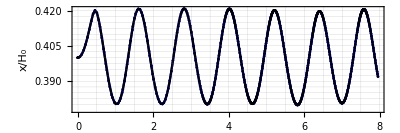
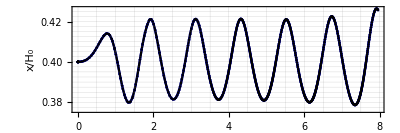
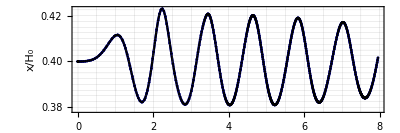
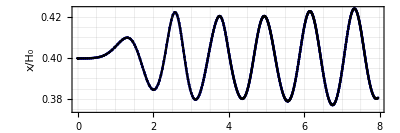

```mathematica
Table[
ListPlot[
{{importGetData[meshC,"simulation_time"],(importGetData[meshC,data,3])}ᵀ,
{importGetData[meshD,"simulation_time"],(importGetData[meshD,data,3])}ᵀ},
Joined->{True,True,True,True,True},
Evaluate[opt],
PlotStyle->plotstyle,
Mesh->All,
PlotRange->{All,All},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->legend,
Evaluate[plot2Doption]
],{data,{"gauge0_intersection","gauge1_intersection","gauge2_intersection","gauge3_intersection"}}]
```

```mathematica
ListPlot[
{{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_pitch"])}ᵀ,
{importGetData[meshD,"simulation_time"],(importGetData[meshD,"float_pitch"])}ᵀ,
{T*#1+shift,k*h#2}&@@@ExperimentData0d04Pitch},
Joined->{True,True,True,True,True},
Evaluate[opt],
PlotStyle->plotstyle,
PlotRange->{{0,12.},All},
PlotRange->{Automatic,Automatic},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["pitch",FontSize->20,FontFamily->"Times"]},
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
]
```

ListPlot::lpn: {{{0.00001,-1.82411×10^-15},{0.00002,-3.5728×10^-15},{0.00003,-5.23605×10^-15},{0.00004,-6.81204×10^-15},{0.00005,-8.29986×10^-15},{0.00006,-9.69891×10^-15},{0.00007,-1.10088×10^-14},{0.00008,-1.22292×10^-14},{0.00009,-1.33599×10^-14},{0.0001,-1.44008×10^-14},{0.00011,-1.53518×10^-14},{0.05011,1.12918×10^-9},«27»,{1.16907,0.000412067},{1.18898,0.000459419},{1.23042,0.00057248},{1.25644,0.000654454},{1.30142,0.000818387},{1.32996,0.000938366},{1.37573,0.00115889},{1.39418,0.00125822},{1.43844,0.00152239},{1.45516,0.00163202},{1.49861,0.00194275},«550»},{«1»},{}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{{{1/100000,-1.82411×10^-15},{1/50000,-3.5728×10^-15},{3/100000,-5.23605×10^-15},{1/25000,-6.81204×10^-15},{1/20000,-8.29986×10^-15},{3/50000,-9.69891×10^-15},{7/100000,-1.10088×10^-14},{1/12500,-1.22292×10^-14},{9/100000,-1.33599×10^-14},{0.0001,-1.44008×10^-14},{0.00011,-1.53518×10^-14},{0.05011,1.12918×10^-9},{0.10011,4.9785×10^-9},{0.15011,1.47239×10^-8},{0.20011,3.89565×10^-8},{0.25011,9.37928×10^-8},{0.30011,2.05766×10^-7},{0.35011,4.1719×10^-7},{0.40011,7.94085×10^-7},{0.45011,1.43626×10^-6},{0.50011,2.49053×10^-6},{0.55011,4.16736×10^-6},{0.583206,5.76492×10^-6},{0.633206,9.19458×10^-6},{0.679492,0.0000138517},{0.691452,0.000015357},{0.739466,0.0000229611},{0.765708,0.0000283798},{0.814112,0.0000413624},{0.844568,0.0000519323},{0.894568,0.0000743928},{0.914457,0.0000854285},{0.964457,0.000119686},{0.972725,0.000126369},{1.00439,0.000155057},{1.04677,0.000202144},{1.06337,0.000223688},{1.10611,0.000288353},{1.12853,0.000328205},{1.16907,0.000412067},{1.18898,0.000459419},{1.23042,0.00057248},{1.25644,0.000654454},{1.30142,0.000818387},{1.32996,0.000938366},{1.37573,0.00115889},{1.39418,0.00125822},{1.43844,0.00152239},{1.45516,0.00163202},{1.49861,0.00194275},{1.5308,0.00219727},{1.56964,0.00253164},{1.59823,0.00279605},{1.64268,0.00323567},{1.68741,0.00370822},{1.71283,0.00398723},{1.75697,0.00448309},{1.77807,0.00472222},{1.82268,0.0052236},{1.83996,0.00541322},{1.88325,0.00586744},{1.90202,0.00605117},{1.94362,0.00641875},{1.97998,0.00668187},{2.00442,0.0068206},{2.04425,0.00696721},{2.08417,0.00699727},{2.12394,0.00689021},{2.15944,0.00666287},{2.19866,0.00625034},{2.23701,0.00566835},{2.27587,0.00488504},{2.31444,0.0039052},{2.35293,0.00272042},{2.39203,0.00130367},{2.43214,-0.00036894},{2.47382,-0.00233103},{2.51661,-0.00456105},{2.55962,-0.00699024},{2.59527,-0.00911517},{2.6264,-0.0110277},{2.65464,-0.0127878},{2.68091,-0.0144278},{2.70579,-0.0159666},{2.72968,-0.0174157},{2.75288,-0.0187818},{2.77566,-0.0200681},{2.79822,-0.0212748},{2.8208,-0.0223992},{2.84359,-0.0234357},{2.86686,-0.0243744},{2.89091,-0.0252},{2.91614,-0.0258882},{2.94313,-0.0263996},{2.97219,-0.0266629},{3.00241,-0.0265915},{3.03257,-0.0261419},{3.06231,-0.0253062},{3.0919,-0.0240717},{3.1215,-0.0224254},{3.15119,-0.0203579},{3.1811,-0.0178591},{3.21139,-0.0149204},{3.23737,-0.0120899},{3.25927,-0.00949734},{3.27865,-0.00706128},{3.29627,-0.00473995},{3.31259,-0.00250868},{3.32792,-0.000351417},{3.34245,0.00174296},{3.35636,0.00378254},{3.36974,0.0057734},{3.38268,0.00772024},{3.39528,0.0096268},{3.40757,0.011496},{3.41962,0.0133304},{3.43148,0.0151318},{3.44318,0.016902},{3.45475,0.0186423},{3.46625,0.0203538},{3.47769,0.0220374},{3.48912,0.0236937},{3.50056,0.0253234},{3.51205,0.0269267},{3.52364,0.0285038},{3.53535,0.0300547},{3.54724,0.0315791},{3.55936,0.0330765},{3.57177,0.0345461},{3.58456,0.0359864},{3.59781,0.0373956},{3.61166,0.0387705},{3.62629,0.0401068},{3.64195,0.041397},{3.65869,0.0426064},{3.67508,0.0436114},{3.6909,0.0444044},{3.70637,0.0450053},{3.72169,0.0454231},{3.73701,0.0456591},{3.7525,0.0457076},{3.76831,0.0455551},{3.7846,0.0451801},{3.80099,0.044576},{3.8175,0.043734},{3.83419,0.0426445},{3.85105,0.0412978},{3.86687,0.0398123},{3.88072,0.0383356},{3.89324,0.0368614},{3.90478,0.035386},{3.91559,0.0339067},{3.92581,0.032422},{3.93555,0.0309305},{3.94489,0.0294309},{3.95391,0.0279225},{3.96265,0.0264044},{3.97115,0.0248757},{3.97946,0.0233358},{3.98759,0.0217841},{3.99557,0.0202197},{4.00343,0.018642},{4.01118,0.0170503},{4.01885,0.015444},{4.02644,0.0138221},{4.03398,0.012184},{4.04147,0.0105289},{4.04894,0.00885571},{4.05639,0.00716363},{4.06383,0.0054516},{4.07129,0.00371849},{4.07876,0.00196308},{4.08627,0.000184019},{4.09384,-0.00162017},{4.10146,-0.00345116},{4.10916,-0.00531079},{4.11696,-0.00720117},{4.12487,-0.00912467},{4.13292,-0.011084},{4.14113,-0.0130824},{4.14953,-0.0151235},{4.15815,-0.0172117},{4.16702,-0.0193523},{4.1762,-0.0215515},{4.18575,-0.0238173},{4.19573,-0.0261597},{4.20626,-0.0285915},{4.21745,-0.0311301},{4.2295,-0.0337994},{4.2427,-0.0366345},{4.25749,-0.0396898},{4.2735,-0.0428344},{4.29013,-0.0458971},{4.30674,-0.0487283},{4.32296,-0.0512572},{4.33872,-0.0534714},{4.35361,-0.0553321},{4.36785,-0.0568891},{4.38157,-0.0581776},{4.3949,-0.0592227},{4.40792,-0.0600428},{4.42073,-0.0606509},{4.43338,-0.0610562},{4.44593,-0.0612643},{4.45803,-0.0612806},{4.46915,-0.061136},{4.47954,-0.0608629},{4.48935,-0.0604833},{4.49869,-0.0600126},{4.50765,-0.0594623},{4.51628,-0.0588412},{4.52463,-0.0581561},{4.53275,-0.0574124},{4.54066,-0.0566147},{4.54839,-0.0557665},{4.55597,-0.0548708},{4.56342,-0.0539301},{4.57075,-0.0529464},{4.57798,-0.0519214},{4.58512,-0.0508567},{4.59218,-0.0497532},{4.59918,-0.0486118},{4.60613,-0.0474334},{4.61304,-0.0462184},{4.61991,-0.0449672},{4.62676,-0.0436798},{4.63359,-0.0423563},{4.64041,-0.0409965},{4.64724,-0.0396},{4.65408,-0.0381664},{4.66095,-0.0366948},{4.66784,-0.0351845},{4.67477,-0.0336341},{4.68175,-0.0320425},{4.68879,-0.0304078},{4.69591,-0.0287281},{4.70312,-0.0270011},{4.71042,-0.0252239},{4.71785,-0.0233933},{4.72541,-0.0215053},{4.73313,-0.0195552},{4.74104,-0.0175373},{4.74917,-0.0154446},{4.75755,-0.0132686},{4.76623,-0.0109986},{4.77527,-0.00862086},{4.78475,-0.00611751},{4.79472,-0.00347486},{4.80465,-0.000843206},{4.81453,0.00177617},{4.82439,0.00438185},{4.83424,0.00697213},{4.84409,0.00954494},{4.85394,0.0120977},{4.86381,0.0146273},{4.87369,0.0171278},{4.88359,0.0195951},{4.8935,0.0220253},{4.90344,0.0244142},{4.91341,0.0267571},{4.9234,0.0290495},{4.93343,0.0312864},{4.94349,0.0334632},{4.95358,0.035575},{4.96372,0.0376171},{4.9739,0.0395848},{4.98413,0.0414734},{4.99442,0.0432784},{5.00477,0.0449954},{5.0142,0.0464712},{5.02281,0.0477402},{5.0308,0.0488503},{5.03831,0.0498327},{5.04543,0.0507099},{5.05226,0.0514979},{5.05884,0.052209},{5.06522,0.0528521},{5.07143,0.0534344},{5.0775,0.0539613},{5.08347,0.054437},{5.0893,0.0548624},{5.0951,0.0552457},{5.10081,0.0555842},{5.10647,0.055882},{5.1121,0.0561397},{5.11764,0.0563568},{5.12311,0.056535},{5.12853,0.0566759},{5.13388,0.0567804},{5.13919,0.05685},{5.14447,0.0568855},{5.14972,0.0568875},{5.15496,0.0568563},{5.1602,0.0567923},{5.16544,0.0566952},{5.1707,0.0565651},{5.17597,0.0564015},{5.18129,0.056203},{5.18665,0.0559695},{5.19206,0.0556998},{5.19752,0.0553929},{5.20305,0.0550472},{5.20866,0.0546609},{5.21436,0.0542327},{5.22016,0.0537593},{5.22608,0.0532373},{5.23216,0.0526628},{5.2384,0.0520311},{5.24484,0.0513367},{5.25151,0.050573},{5.25843,0.0497322},{5.26566,0.0488049},{5.27323,0.0477794},{5.28113,0.0466526},{5.28929,0.0454307},{5.29775,0.0441039},{5.30656,0.04266},{5.31578,0.0410837},{5.3255,0.0393551},{5.33582,0.0374479},{5.3469,0.0353263},{5.35896,0.0329388},{5.37232,0.0302074},{5.38572,0.0273906},{5.39911,0.0245095},{5.41254,0.0215734},{5.42597,0.018599},{5.43918,0.0156517},{5.45212,0.012755},{5.46465,0.00995421},{5.47655,0.00730821},{5.48794,0.00479358},{5.49894,0.00239302},{5.50962,0.0000933928},{5.52004,-0.0021156},{5.53026,-0.00424214},{5.54031,-0.00629282},{5.55024,-0.00827304},{5.56008,-0.0101872},{5.56986,-0.0120389},{5.57962,-0.0138311},{5.58938,-0.0155663},{5.59917,-0.0172462},{5.60902,-0.0188722},{5.61896,-0.0204454},{5.62902,-0.0219662},{5.63924,-0.0234347},{5.64966,-0.0248504},{5.66033,-0.0262122},{5.6713,-0.0275184},{5.68257,-0.0287593},{5.69369,-0.0298819},{5.7047,-0.0308932},{5.71564,-0.0317989},{5.72656,-0.032603},{5.73748,-0.0333083},{5.74845,-0.0339168},{5.75948,-0.0344292},{5.77063,-0.0348458},{5.78193,-0.0351655},{5.7934,-0.0353866},{5.80472,-0.035504},{5.81569,-0.0355245},{5.8264,-0.035458},{5.83689,-0.0353121},{5.84722,-0.0350927},{5.85741,-0.0348044},{5.86752,-0.0344507},{5.87757,-0.0340342},{5.88755,-0.0335589},{5.89744,-0.0330304},{5.90724,-0.0324516},{5.91698,-0.0318253},{5.92668,-0.0311535},{5.93634,-0.0304383},{5.94599,-0.0296812},{5.95564,-0.0288839},{5.96529,-0.0280478},{5.97498,-0.0271743},{5.98469,-0.0262648},{5.99445,-0.0253206},{6.00426,-0.0243433},{6.01413,-0.0233343},{6.02406,-0.0222961},{6.03404,-0.0212317},{6.04408,-0.0201436},{6.05418,-0.0190341},{6.06433,-0.0179057},{6.07455,-0.0167612},{6.08483,-0.0156032},{6.09518,-0.0144343},{6.1056,-0.013257},{6.1161,-0.0120736},{6.12669,-0.0108862},{6.13739,-0.00969697},{6.1482,-0.00850783},{6.15914,-0.00732085},{6.17019,-0.00614261},{6.18016,-0.0051008},{6.18941,-0.0041528},{6.19793,-0.00329775},{6.20602,-0.00250393},{6.21362,-0.0017751},{6.22087,-0.00109504},{6.22784,-0.000456619},{6.23457,0.000145501},{6.24112,0.000715583},{6.24749,0.00125704},{6.25373,0.00177261},{6.25985,0.00226452},{6.26588,0.00273461},{6.27181,0.00318437},{6.27768,0.00361503},{6.28349,0.00402762},{6.28925,0.004423},{6.29497,0.00480188},{6.30067,0.00516485},{6.30633,0.00551242},{6.31199,0.00584502},{6.31763,0.00616301},{6.32327,0.00646669},{6.32892,0.0067563},{6.33459,0.00703202},{6.34027,0.00729396},{6.34599,0.00754221},{6.35174,0.00777683},{6.35754,0.00799777},{6.3634,0.00820492},{6.36931,0.00839807},{6.3753,0.00857697},{6.38138,0.00874125},{6.38754,0.00889051},{6.3938,0.00902425},{6.40019,0.00914202},{6.40669,0.00924288},{6.41333,0.0093263},{6.42013,0.00939126},{6.4271,0.00943678},{6.43425,0.0094617},{6.44161,0.0094647},{6.44919,0.00944427},{6.45704,0.00939866},{6.46518,0.0093258},{6.47365,0.00922333},{6.48248,0.00908854},{6.49173,0.00891836},{6.50144,0.00870929},{6.51167,0.00845733},{6.52249,0.00815805},{6.53398,0.00780656},{6.54618,0.00739951},{6.5589,0.00694308},{6.57202,0.00644272},{6.58509,0.00592092},{6.59812,0.00538344},{6.61113,0.00483573},{6.62413,0.00428306},{6.63715,0.00373057},{6.65021,0.00318334},{6.66334,0.00264645},{6.67655,0.00212512},{6.68967,0.00163215},{6.7026,0.00117597},{6.71539,0.000758445},{6.72808,0.000381637},{6.74073,0.0000477842},{6.75336,-0.000240683},{6.76602,-0.000481119},{6.77874,-0.000670608},{6.79157,-0.00080591},{6.80455,-0.000883402},{6.81771,-0.000898999},{6.83111,-0.000848086},{6.84478,-0.000725461},{6.85878,-0.000525312},{6.8722,-0.00026254},{6.88475,0.0000455697},{6.89662,0.000391747},{6.90795,0.000770761},{6.91884,0.00117869},{6.92937,0.00161252},{6.93959,0.00206984},{6.94957,0.00254873},{6.95933,0.00304761},{6.96892,0.00356519},{6.97836,0.0041004},{6.98769,0.00465235},{6.99693,0.0052203},{7.00611,0.00580364},{7.01523,0.0064019},{7.02434,0.00701468},{7.03344,0.0076417},{7.04255,0.00828277},{7.05171,0.00893778},{7.06092,0.00960674},{7.07022,0.0102897},{7.07963,0.0109869},{7.08918,0.0116987},{7.0989,0.0124254},{7.10884,0.0131677},{7.11902,0.0139263},{7.12952,0.0147023},{7.14039,0.015497},{7.15151,0.0162971},{7.16262,0.0170792},{7.17373,0.0178417},{7.18488,0.0185829},{7.19611,0.0193012},{7.20744,0.0199949},{7.21893,0.0206616},{7.23043,0.0212886},{7.24196,0.0218731},{7.25351,0.0224106},{7.2651,0.0228979},{7.27675,0.0233316},{7.28848,0.0237081},{7.30031,0.024023},{7.31225,0.0242716},{7.32434,0.0244489},{7.33657,0.024549},{7.34898,0.0245655},{7.36159,0.0244917},{7.3744,0.0243201},{7.38742,0.0240428},{7.39863,0.0237193},{7.40828,0.0233769},{7.41686,0.0230218},{7.42468,0.022657},{7.4319,0.0222838},{7.43868,0.0219026},{7.4451,0.0215135},{7.45123,0.0211164},{7.45712,0.0207113},{7.46281,0.0202981},{7.46834,0.0198765},{7.47372,0.0194465},{7.47897,0.019008},{7.48412,0.0185607},{7.48917,0.0181045},{7.49412,0.0176421},{7.49903,0.0171671},{7.50385,0.0166853},{7.50863,0.0161934},{7.51337,0.0156908},{7.51808,0.0151772},{7.52277,0.0146521},{7.52744,0.0141152},{7.53211,0.0135659},{7.53677,0.0130039},{7.54143,0.0124285},{7.5461,0.0118393},{7.55078,0.0112355},{7.55548,0.0106166},{7.5602,0.00998188},{7.56495,0.00933052},{7.56974,0.00866174},{7.57457,0.00797467},{7.57944,0.00726921},{7.58437,0.00654366},{7.58935,0.00579677},{7.5944,0.0050273},{7.59953,0.00423398},{7.60474,0.00341548},{7.61003,0.00257045},{7.61543,0.00169738},{7.62094,0.000792267},{7.62656,-0.000141932},{7.63232,-0.00111176},{7.63821,-0.00211707},{7.64425,-0.00316029},{7.65047,-0.00424417},{7.65686,-0.00537204},{7.66346,-0.0065478},{7.6703,-0.00777599},{7.67739,-0.009061},{7.68479,-0.0104103},{7.69252,-0.0118306},{7.70064,-0.0133298},{7.70921,-0.0149159},{7.71801,-0.0165496},{7.72709,-0.0182348},{7.73649,-0.019976},{7.74626,-0.0217785},{7.75648,-0.0236491},{7.76723,-0.0255959},{7.77862,-0.0276296},{7.7908,-0.0297638},{7.80324,-0.0318883},{7.8157,-0.0339555},{7.82821,-0.0359572},{7.84076,-0.037885},{7.85338,-0.0397301},{7.86605,-0.0414833},{7.8787,-0.0431251},{7.89116,-0.0446271},{7.90347,-0.0459935},{7.91568,-0.0472267},{7.92785,-0.0483278},{7.94,-0.0492965},{7.95212,-0.0501262}},{{1/100000,-1.82411×10^-15},{1/50000,-3.5728×10^-15},{3/100000,-5.23605×10^-15},{1/25000,-6.81204×10^-15},{1/20000,-8.29986×10^-15},{3/50000,-9.69891×10^-15},{7/100000,-1.10088×10^-14},{1/12500,-1.22292×10^-14},{9/100000,-1.33599×10^-14},{0.0001,-1.44008×10^-14},{0.00011,-1.53518×10^-14},{0.05011,1.12918×10^-9},{0.10011,4.9785×10^-9},{0.15011,1.47239×10^-8},{0.20011,3.89565×10^-8},{0.25011,9.37928×10^-8},{0.30011,2.05766×10^-7},{0.35011,4.1719×10^-7},{0.40011,7.94085×10^-7},{0.45011,1.43626×10^-6},{0.50011,2.49053×10^-6},{0.55011,4.16736×10^-6},{0.583206,5.76492×10^-6},{0.633206,9.19458×10^-6},{0.679492,0.0000138517},{0.691452,0.000015357},{0.739466,0.0000229611},{0.765708,0.0000283798},{0.814112,0.0000413624},{0.844568,0.0000519323},{0.894568,0.0000743928},{0.914457,0.0000854285},{0.964457,0.000119686},{0.972725,0.000126369},{1.00439,0.000155057},{1.04677,0.000202144},{1.06337,0.000223688},{1.10611,0.000288353},{1.12853,0.000328205},{1.16907,0.000412067},{1.18898,0.000459419},{1.23042,0.00057248},{1.25644,0.000654454},{1.30142,0.000818387},{1.32996,0.000938366},{1.37573,0.00115889},{1.39418,0.00125822},{1.43844,0.00152239},{1.45516,0.00163202},{1.49861,0.00194275},{1.5308,0.00219727},{1.56964,0.00253164},{1.59823,0.00279605},{1.64268,0.00323567},{1.68741,0.00370822},{1.71283,0.00398723},{1.75697,0.00448309},{1.77807,0.00472222},{1.82268,0.0052236},{1.83996,0.00541322},{1.88325,0.00586744},{1.90202,0.00605117},{1.94362,0.00641875},{1.97998,0.00668187},{2.00442,0.0068206},{2.04425,0.00696721},{2.08417,0.00699727},{2.12394,0.00689021},{2.15944,0.00666287},{2.19866,0.00625034},{2.23701,0.00566835},{2.27587,0.00488504},{2.31444,0.0039052},{2.35293,0.00272042},{2.39203,0.00130367},{2.43214,-0.00036894},{2.47382,-0.00233103},{2.51661,-0.00456105},{2.55962,-0.00699024},{2.59527,-0.00911517},{2.6264,-0.0110277},{2.65464,-0.0127878},{2.68091,-0.0144278},{2.70579,-0.0159666},{2.72968,-0.0174157},{2.75288,-0.0187818},{2.77566,-0.0200681},{2.79822,-0.0212748},{2.8208,-0.0223992},{2.84359,-0.0234357},{2.86686,-0.0243744},{2.89091,-0.0252},{2.91614,-0.0258882},{2.94313,-0.0263996},{2.97219,-0.0266629},{3.00241,-0.0265915},{3.03257,-0.0261419},{3.06231,-0.0253062},{3.0919,-0.0240717},{3.1215,-0.0224254},{3.15119,-0.0203579},{3.1811,-0.0178591},{3.21139,-0.0149204},{3.23737,-0.0120899},{3.25927,-0.00949734},{3.27865,-0.00706128},{3.29627,-0.00473995},{3.31259,-0.00250868},{3.32792,-0.000351417},{3.34245,0.00174296},{3.35636,0.00378254},{3.36974,0.0057734},{3.38268,0.00772024},{3.39528,0.0096268},{3.40757,0.011496},{3.41962,0.0133304},{3.43148,0.0151318},{3.44318,0.016902},{3.45475,0.0186423},{3.46625,0.0203538},{3.47769,0.0220374},{3.48912,0.0236937},{3.50056,0.0253234},{3.51205,0.0269267},{3.52364,0.0285038},{3.53535,0.0300547},{3.54724,0.0315791},{3.55936,0.0330765},{3.57177,0.0345461},{3.58456,0.0359864},{3.59781,0.0373956},{3.61166,0.0387705},{3.62629,0.0401068},{3.64195,0.041397},{3.65869,0.0426064},{3.67508,0.0436114},{3.6909,0.0444044},{3.70637,0.0450053},{3.72169,0.0454231},{3.73701,0.0456591},{3.7525,0.0457076},{3.76831,0.0455551},{3.7846,0.0451801},{3.80099,0.044576},{3.8175,0.043734},{3.83419,0.0426445},{3.85105,0.0412978},{3.86687,0.0398123},{3.88072,0.0383356},{3.89324,0.0368614},{3.90478,0.035386},{3.91559,0.0339067},{3.92581,0.032422},{3.93555,0.0309305},{3.94489,0.0294309},{3.95391,0.0279225},{3.96265,0.0264044},{3.97115,0.0248757},{3.97946,0.0233358},{3.98759,0.0217841},{3.99557,0.0202197},{4.00343,0.018642},{4.01118,0.0170503},{4.01885,0.015444},{4.02644,0.0138221},{4.03398,0.012184},{4.04147,0.0105289},{4.04894,0.00885571},{4.05639,0.00716363},{4.06383,0.0054516},{4.07129,0.00371849},{4.07876,0.00196308},{4.08627,0.000184019},{4.09384,-0.00162017},{4.10146,-0.00345116},{4.10916,-0.00531079},{4.11696,-0.00720117},{4.12487,-0.00912467},{4.13292,-0.011084},{4.14113,-0.0130824},{4.14953,-0.0151235},{4.15815,-0.0172117},{4.16702,-0.0193523},{4.1762,-0.0215515},{4.18575,-0.0238173},{4.19573,-0.0261597},{4.20626,-0.0285915},{4.21745,-0.0311301},{4.2295,-0.0337994},{4.2427,-0.0366345},{4.25749,-0.0396898},{4.2735,-0.0428344},{4.29013,-0.0458971},{4.30674,-0.0487283},{4.32296,-0.0512572},{4.33872,-0.0534714},{4.35361,-0.0553321},{4.36785,-0.0568891},{4.38157,-0.0581776},{4.3949,-0.0592227},{4.40792,-0.0600428},{4.42073,-0.0606509},{4.43338,-0.0610562},{4.44593,-0.0612643},{4.45803,-0.0612806},{4.46915,-0.061136},{4.47954,-0.0608629},{4.48935,-0.0604833},{4.49869,-0.0600126},{4.50765,-0.0594623},{4.51628,-0.0588412},{4.52463,-0.0581561},{4.53275,-0.0574124},{4.54066,-0.0566147},{4.54839,-0.0557665},{4.55597,-0.0548708},{4.56342,-0.0539301},{4.57075,-0.0529464},{4.57798,-0.0519214},{4.58512,-0.0508567},{4.59218,-0.0497532},{4.59918,-0.0486118},{4.60613,-0.0474334},{4.61304,-0.0462184},{4.61991,-0.0449672},{4.62676,-0.0436798},{4.63359,-0.0423563},{4.64041,-0.0409965},{4.64724,-0.0396},{4.65408,-0.0381664},{4.66095,-0.0366948},{4.66784,-0.0351845},{4.67477,-0.0336341},{4.68175,-0.0320425},{4.68879,-0.0304078},{4.69591,-0.0287281},{4.70312,-0.0270011},{4.71042,-0.0252239},{4.71785,-0.0233933},{4.72541,-0.0215053},{4.73313,-0.0195552},{4.74104,-0.0175373},{4.74917,-0.0154446},{4.75755,-0.0132686},{4.76623,-0.0109986},{4.77527,-0.00862086},{4.78475,-0.00611751},{4.79472,-0.00347486},{4.80465,-0.000843206},{4.81453,0.00177617},{4.82439,0.00438185},{4.83424,0.00697213},{4.84409,0.00954494},{4.85394,0.0120977},{4.86381,0.0146273},{4.87369,0.0171278},{4.88359,0.0195951},{4.8935,0.0220253},{4.90344,0.0244142},{4.91341,0.0267571},{4.9234,0.0290495},{4.93343,0.0312864},{4.94349,0.0334632},{4.95358,0.035575},{4.96372,0.0376171},{4.9739,0.0395848},{4.98413,0.0414734},{4.99442,0.0432784},{5.00477,0.0449954},{5.0142,0.0464712},{5.02281,0.0477402},{5.0308,0.0488503},{5.03831,0.0498327},{5.04543,0.0507099},{5.05226,0.0514979},{5.05884,0.052209},{5.06522,0.0528521},{5.07143,0.0534344},{5.0775,0.0539613},{5.08347,0.054437},{5.0893,0.0548624},{5.0951,0.0552457},{5.10081,0.0555842},{5.10647,0.055882},{5.1121,0.0561397},{5.11764,0.0563568},{5.12311,0.056535},{5.12853,0.0566759},{5.13388,0.0567804},{5.13919,0.05685},{5.14447,0.0568855},{5.14972,0.0568875},{5.15496,0.0568563},{5.1602,0.0567923},{5.16544,0.0566952},{5.1707,0.0565651},{5.17597,0.0564015},{5.18129,0.056203},{5.18665,0.0559695},{5.19206,0.0556998},{5.19752,0.0553929},{5.20305,0.0550472},{5.20866,0.0546609},{5.21436,0.0542327},{5.22016,0.0537593},{5.22608,0.0532373},{5.23216,0.0526628},{5.2384,0.0520311},{5.24484,0.0513367},{5.25151,0.050573},{5.25843,0.0497322},{5.26566,0.0488049},{5.27323,0.0477794},{5.28113,0.0466526},{5.28929,0.0454307},{5.29775,0.0441039},{5.30656,0.04266},{5.31578,0.0410837},{5.3255,0.0393551},{5.33582,0.0374479},{5.3469,0.0353263},{5.35896,0.0329388},{5.37232,0.0302074},{5.38572,0.0273906},{5.39911,0.0245095},{5.41254,0.0215734},{5.42597,0.018599},{5.43918,0.0156517},{5.45212,0.012755},{5.46465,0.00995421},{5.47655,0.00730821},{5.48794,0.00479358},{5.49894,0.00239302},{5.50962,0.0000933928},{5.52004,-0.0021156},{5.53026,-0.00424214},{5.54031,-0.00629282},{5.55024,-0.00827304},{5.56008,-0.0101872},{5.56986,-0.0120389},{5.57962,-0.0138311},{5.58938,-0.0155663},{5.59917,-0.0172462},{5.60902,-0.0188722},{5.61896,-0.0204454},{5.62902,-0.0219662},{5.63924,-0.0234347},{5.64966,-0.0248504},{5.66033,-0.0262122},{5.6713,-0.0275184},{5.68257,-0.0287593},{5.69369,-0.0298819},{5.7047,-0.0308932},{5.71564,-0.0317989},{5.72656,-0.032603},{5.73748,-0.0333083},{5.74845,-0.0339168},{5.75948,-0.0344292},{5.77063,-0.0348458},{5.78193,-0.0351655},{5.7934,-0.0353866},{5.80472,-0.035504},{5.81569,-0.0355245},{5.8264,-0.035458},{5.83689,-0.0353121},{5.84722,-0.0350927},{5.85741,-0.0348044},{5.86752,-0.0344507},{5.87757,-0.0340342},{5.88755,-0.0335589},{5.89744,-0.0330304},{5.90724,-0.0324516},{5.91698,-0.0318253},{5.92668,-0.0311535},{5.93634,-0.0304383},{5.94599,-0.0296812},{5.95564,-0.0288839},{5.96529,-0.0280478},{5.97498,-0.0271743},{5.98469,-0.0262648},{5.99445,-0.0253206},{6.00426,-0.0243433},{6.01413,-0.0233343},{6.02406,-0.0222961},{6.03404,-0.0212317},{6.04408,-0.0201436},{6.05418,-0.0190341},{6.06433,-0.0179057},{6.07455,-0.0167612},{6.08483,-0.0156032},{6.09518,-0.0144343},{6.1056,-0.013257},{6.1161,-0.0120736},{6.12669,-0.0108862},{6.13739,-0.00969697},{6.1482,-0.00850783},{6.15914,-0.00732085},{6.17019,-0.00614261},{6.18016,-0.0051008},{6.18941,-0.0041528},{6.19793,-0.00329775},{6.20602,-0.00250393},{6.21362,-0.0017751},{6.22087,-0.00109504},{6.22784,-0.000456619},{6.23457,0.000145501},{6.24112,0.000715583},{6.24749,0.00125704},{6.25373,0.00177261},{6.25985,0.00226452},{6.26588,0.00273461},{6.27181,0.00318437},{6.27768,0.00361503},{6.28349,0.00402762},{6.28925,0.004423},{6.29497,0.00480188},{6.30067,0.00516485},{6.30633,0.00551242},{6.31199,0.00584502},{6.31763,0.00616301},{6.32327,0.00646669},{6.32892,0.0067563},{6.33459,0.00703202},{6.34027,0.00729396},{6.34599,0.00754221},{6.35174,0.00777683},{6.35754,0.00799777},{6.3634,0.00820492},{6.36931,0.00839807},{6.3753,0.00857697},{6.38138,0.00874125},{6.38754,0.00889051},{6.3938,0.00902425},{6.40019,0.00914202},{6.40669,0.00924288},{6.41333,0.0093263},{6.42013,0.00939126},{6.4271,0.00943678},{6.43425,0.0094617},{6.44161,0.0094647},{6.44919,0.00944427},{6.45704,0.00939866},{6.46518,0.0093258},{6.47365,0.00922333},{6.48248,0.00908854},{6.49173,0.00891836},{6.50144,0.00870929},{6.51167,0.00845733},{6.52249,0.00815805},{6.53398,0.00780656},{6.54618,0.00739951},{6.5589,0.00694308},{6.57202,0.00644272},{6.58509,0.00592092},{6.59812,0.00538344},{6.61113,0.00483573},{6.62413,0.00428306},{6.63715,0.00373057},{6.65021,0.00318334},{6.66334,0.00264645},{6.67655,0.00212512},{6.68967,0.00163215},{6.7026,0.00117597},{6.71539,0.000758445},{6.72808,0.000381637},{6.74073,0.0000477842},{6.75336,-0.000240683},{6.76602,-0.000481119},{6.77874,-0.000670608},{6.79157,-0.00080591},{6.80455,-0.000883402},{6.81771,-0.000898999},{6.83111,-0.000848086},{6.84478,-0.000725461},{6.85878,-0.000525312},{6.8722,-0.00026254},{6.88475,0.0000455697},{6.89662,0.000391747},{6.90795,0.000770761},{6.91884,0.00117869},{6.92937,0.00161252},{6.93959,0.00206984},{6.94957,0.00254873},{6.95933,0.00304761},{6.96892,0.00356519},{6.97836,0.0041004},{6.98769,0.00465235},{6.99693,0.0052203},{7.00611,0.00580364},{7.01523,0.0064019},{7.02434,0.00701468},{7.03344,0.0076417},{7.04255,0.00828277},{7.05171,0.00893778},{7.06092,0.00960674},{7.07022,0.0102897},{7.07963,0.0109869},{7.08918,0.0116987},{7.0989,0.0124254},{7.10884,0.0131677},{7.11902,0.0139263},{7.12952,0.0147023},{7.14039,0.015497},{7.15151,0.0162971},{7.16262,0.0170792},{7.17373,0.0178417},{7.18488,0.0185829},{7.19611,0.0193012},{7.20744,0.0199949},{7.21893,0.0206616},{7.23043,0.0212886},{7.24196,0.0218731},{7.25351,0.0224106},{7.2651,0.0228979},{7.27675,0.0233316},{7.28848,0.0237081},{7.30031,0.024023},{7.31225,0.0242716},{7.32434,0.0244489},{7.33657,0.024549},{7.34898,0.0245655},{7.36159,0.0244917},{7.3744,0.0243201},{7.38742,0.0240428},{7.39863,0.0237193},{7.40828,0.0233769},{7.41686,0.0230218},{7.42468,0.022657},{7.4319,0.0222838},{7.43868,0.0219026},{7.4451,0.0215135},{7.45123,0.0211164},{7.45712,0.0207113},{7.46281,0.0202981},{7.46834,0.0198765},{7.47372,0.0194465},{7.47897,0.019008},{7.48412,0.0185607},{7.48917,0.0181045},{7.49412,0.0176421},{7.49903,0.0171671},{7.50385,0.0166853},{7.50863,0.0161934},{7.51337,0.0156908},{7.51808,0.0151772},{7.52277,0.0146521},{7.52744,0.0141152},{7.53211,0.0135659},{7.53677,0.0130039},{7.54143,0.0124285},{7.5461,0.0118393},{7.55078,0.0112355},{7.55548,0.0106166},{7.5602,0.00998188},{7.56495,0.00933052},{7.56974,0.00866174},{7.57457,0.00797467},{7.57944,0.00726921},{7.58437,0.00654366},{7.58935,0.00579677},{7.5944,0.0050273},{7.59953,0.00423398},{7.60474,0.00341548},{7.61003,0.00257045},{7.61543,0.00169738},{7.62094,0.000792267},{7.62656,-0.000141932},{7.63232,-0.00111176},{7.63821,-0.00211707},{7.64425,-0.00316029},{7.65047,-0.00424417},{7.65686,-0.00537204},{7.66346,-0.0065478},{7.6703,-0.00777599},{7.67739,-0.009061},{7.68479,-0.0104103},{7.69252,-0.0118306},{7.70064,-0.0133298},{7.70921,-0.0149159},{7.71801,-0.0165496},{7.72709,-0.0182348},{7.73649,-0.019976},{7.74626,-0.0217785},{7.75648,-0.0236491},{7.76723,-0.0255959},{7.77862,-0.0276296},{7.7908,-0.0297638},{7.80324,-0.0318883},{7.8157,-0.0339555},{7.82821,-0.0359572},{7.84076,-0.037885},{7.85338,-0.0397301},{7.86605,-0.0414833},{7.8787,-0.0431251},{7.89116,-0.0446271},{7.90347,-0.0459935},{7.91568,-0.0472267},{7.92785,-0.0483278},{7.94,-0.0492965},{7.95212,-0.0501262}},$Failed},Joined→{True,True,True,True,True},{FrameStyle→Directive[FontSize→16,GrayLevel[0],Thickness[0.002]],GridLines→All,GridLinesStyle→Directive[GrayLevel[0.5],AbsoluteThickness[0.001]],ImageSize→400,PlotStyle→{{RGBColor[0, 0, 1]},{GrayLevel[0]},{RGBColor[1, 0, 0]}},AspectRatio→1/3},PlotStyle→{{RGBColor[1, 0, 0],Dashing[{Small,Small}]},{RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],Dashing[{Small,Small}]},{RGBColor[1, 0.5, 0]},{RGBColor[1, 0, 1]},{GrayLevel[0]}},PlotRange→{{0,12.},All},PlotRange→{Automatic,Automatic},FrameLabel→{t/T,pitch},PlotLegends→Placed[LineLegend[{mesh A,mesh B,mesh C,mesh D,mesh E,Exp (Ren et al., 2015)},LegendMarkerSize→20,LabelStyle→10],{0.65,0.15}],{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

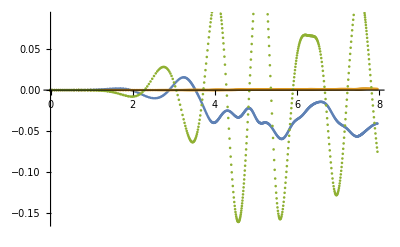

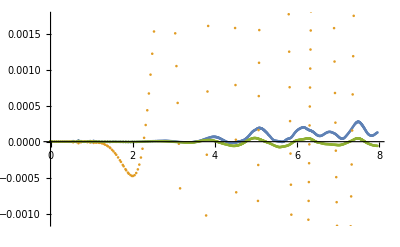

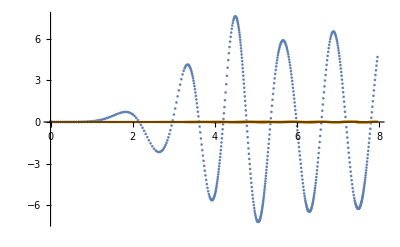

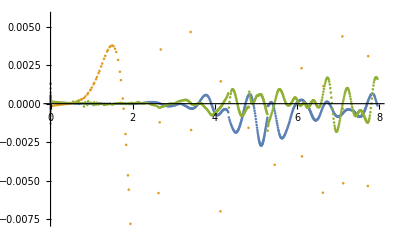

```mathematica
ListPlot[
{{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_drag_force",1])}ᵀ,
{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_drag_force",2])}ᵀ,
{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_drag_force",3])}ᵀ}
]
ListPlot[
{{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_drag_torque",1])}ᵀ,
{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_drag_torque",2])}ᵀ,
{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_drag_torque",3])}ᵀ}
]
ListPlot[
{{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_force",1])}ᵀ,
{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_force",2])}ᵀ(*,
{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_force",3])}ᵀ*)}
]
ListPlot[
{{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_torque",1])}ᵀ,
{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_torque",2])}ᵀ,
{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_torque",3])}ᵀ}
]
```

## あるケースの結果

```mathematica
opt={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->400,
PlotStyle->{{Blue},(*{Black},*){Red}},
AspectRatio->1/5};
plotxrange={1,12};
```

```mathematica
shift=4.5-1.2
```

3.3

```mathematica
mesh="meshA";
name="/Users/tomoaki/BEM/Cheng2018_H0d04_T1d2_piston_with_float_ALE1/result.json"
```

/Users/tomoaki/BEM/Cheng2018_H0d04_T1d2_piston_with_float_ALE1/result.json

```mathematica
Manipulate[
ListPlot[
{{importGetData[name,"float_COM",1],importGetData[name,"float_COM",3]-0.4}ᵀ
(*,{#1,#2}&@@@ExperimentData,*)
(*,Table[drift,{t,0,10,0.01}]*)
,{#1+shift,#2}&@@@ExperimentData0d04},
PlotRange->All,
Joined->{True,True,False},
PlotStyle->{{Red},{Blue,Dashed}},
PlotRange->{Automatic,Automatic},
PlotLabel->shift,
FrameLabel->{Style["x",FontSize->20,FontFamily->"Times",Italic],Style["y",FontSize->16,FontFamily->"Times",Italic]},
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
],{shift,3.3882,3.5}]
```

ListPlot::lpn: {{{3.35,0.},{3.35,0.},{3.35,0.},{3.35,0.},{3.35,0.},{3.35,0.},{3.35,0.},{3.35,0.},{3.35,0.},{3.35,0.},{3.35,0.},{3.35,0.},{3.35,0.},{3.35,0.},«23»,{3.35017,0.00022},{3.3502,0.000251},{3.35026,0.000317},{3.35029,0.000355},{3.35038,0.000445},{3.35044,0.000511},{3.35057,0.000643},{3.35068,0.000741},{3.35087,0.000922},{3.35097,0.001005},{3.35122,0.001225},{3.35133,0.001318},{3.35165,0.001582},«550»},{}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

```mathematica
fig=ListPlot[
{{(importGetData[name,"simulation_time"]),(importGetData[name,"float_COM",3]-0.4)}ᵀ,
{T*#1+shift,h#2}&@@@ExperimentData0d04Heave},
Joined->{True,True},
PlotRange->{plotxrange,{-0.03,0.03}},
FrameLabel->{(*Style["t [s]",FontSize->16,FontFamily->"Times"]*)None,Style["z [m]",FontSize->16,FontFamily->"Times"]},
Evaluate[opt],
Evaluate[plot2Doption]
]
Export[FileNameJoin[{NotebookDirectory[],mesh<>"_t_vs_z_Ren2015.jpg"}],%,ImageResolution->150];
```

ListPlot::lpn: {{{0.00001,0.},{0.00002,0.},{0.00003,0.},{0.00004,0.},{0.00005,0.},{0.00006,0.},{0.00007,0.},{0.00008,0.},{0.00009,0.},{0.0001,0.},{0.00011,0.},{0.05011,0.},{0.10011,0.},«25»,{1.12853,0.000251},{1.16907,0.000317},{1.18898,0.000355},{1.23042,0.000445},{1.25644,0.000511},{1.30142,0.000643},{1.32996,0.000741},{1.37573,0.000922},{1.39418,0.001005},{1.43844,0.001225},{1.45516,0.001318},{1.49861,0.001582},«550»},{}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{{{1/100000,0.},{1/50000,0.},{3/100000,0.},{1/25000,0.},{1/20000,0.},{3/50000,0.},{7/100000,0.},{1/12500,0.},{9/100000,0.},{0.0001,0.},{0.00011,0.},{0.05011,0.},{0.10011,0.},{0.15011,0.},{0.20011,0.},{0.25011,0.},{0.30011,0.},{0.35011,0.},{0.40011,0.},{0.45011,1.×10^-6},{0.50011,1.×10^-6},{0.55011,2.×10^-6},{0.583206,3.×10^-6},{0.633206,6.×10^-6},{0.679492,9.×10^-6},{0.691452,0.00001},{0.739466,0.000015},{0.765708,0.000019},{0.814112,0.000029},{0.844568,0.000037},{0.894568,0.000054},{0.914457,0.000062},{0.964457,0.000088},{0.972725,0.000094},{1.00439,0.000116},{1.04677,0.000152},{1.06337,0.000169},{1.10611,0.00022},{1.12853,0.000251},{1.16907,0.000317},{1.18898,0.000355},{1.23042,0.000445},{1.25644,0.000511},{1.30142,0.000643},{1.32996,0.000741},{1.37573,0.000922},{1.39418,0.001005},{1.43844,0.001225},{1.45516,0.001318},{1.49861,0.001582},{1.5308,0.001802},{1.56964,0.002094},{1.59823,0.002329},{1.64268,0.002725},{1.68741,0.003162},{1.71283,0.003426},{1.75697,0.003908},{1.77807,0.004146},{1.82268,0.004665},{1.83996,0.004868},{1.88325,0.005379},{1.90202,0.005599},{1.94362,0.006072},{1.97998,0.006462},{2.00442,0.006706},{2.04425,0.007062},{2.08417,0.007354},{2.12394,0.007563},{2.15944,0.007667},{2.19866,0.007679},{2.23701,0.007573},{2.27587,0.007335},{2.31444,0.006959},{2.35293,0.006439},{2.39203,0.005759},{2.43214,0.004904},{2.47382,0.003853},{2.51661,0.002616},{2.55962,0.001232},{2.59527,-1.×10^-6},{2.6264,-0.001123},{2.65464,-0.002166},{2.68091,-0.003144},{2.70579,-0.004066},{2.72968,-0.004939},{2.75288,-0.005767},{2.77566,-0.00655},{2.79822,-0.007288},{2.8208,-0.007982},{2.84359,-0.008628},{2.86686,-0.009221},{2.89091,-0.009754},{2.91614,-0.010216},{2.94313,-0.010587},{2.97219,-0.010831},{3.00241,-0.010899},{3.03257,-0.010766},{3.06231,-0.010428},{3.0919,-0.009883},{3.1215,-0.009127},{3.15119,-0.008158},{3.1811,-0.006975},{3.21139,-0.005578},{3.23737,-0.004234},{3.25927,-0.003005},{3.27865,-0.001856},{3.29627,-0.000766},{3.31259,0.000275},{3.32792,0.001276},{3.34245,0.00224},{3.35636,0.003172},{3.36974,0.004074},{3.38268,0.004948},{3.39528,0.005796},{3.40757,0.006618},{3.41962,0.007415},{3.43148,0.008187},{3.44318,0.008936},{3.45475,0.00966},{3.46625,0.01036},{3.47769,0.011035},{3.48912,0.011684},{3.50056,0.012308},{3.51205,0.012905},{3.52364,0.013473},{3.53535,0.014012},{3.54724,0.014518},{3.55936,0.01499},{3.57177,0.015424},{3.58456,0.015815},{3.59781,0.016159},{3.61166,0.016447},{3.62629,0.016669},{3.64195,0.016809},{3.65869,0.016843},{3.67508,0.016757},{3.6909,0.016561},{3.70637,0.016258},{3.72169,0.01585},{3.73701,0.015334},{3.7525,0.014704},{3.76831,0.013949},{3.7846,0.013056},{3.80099,0.012044},{3.8175,0.010912},{3.83419,0.009662},{3.85105,0.008296},{3.86687,0.006929},{3.88072,0.00567},{3.89324,0.004488},{3.90478,0.003364},{3.91559,0.002287},{3.92581,0.001249},{3.93555,0.000244},{3.94489,-0.000732},{3.95391,-0.001681},{3.96265,-0.002607},{3.97115,-0.003512},{3.97946,-0.004396},{3.98759,-0.005262},{3.99557,-0.00611},{4.00343,-0.006942},{4.01118,-0.007757},{4.01885,-0.008558},{4.02644,-0.009343},{4.03398,-0.010113},{4.04147,-0.01087},{4.04894,-0.011612},{4.05639,-0.01234},{4.06383,-0.013053},{4.07129,-0.013753},{4.07876,-0.014438},{4.08627,-0.015108},{4.09384,-0.015764},{4.10146,-0.016404},{4.10916,-0.017028},{4.11696,-0.017635},{4.12487,-0.018225},{4.13292,-0.018796},{4.14113,-0.019347},{4.14953,-0.019876},{4.15815,-0.020382},{4.16702,-0.020862},{4.1762,-0.021314},{4.18575,-0.021732},{4.19573,-0.022113},{4.20626,-0.02245},{4.21745,-0.022733},{4.2295,-0.022949},{4.2427,-0.023077},{4.25749,-0.023085},{4.2735,-0.022929},{4.29013,-0.022584},{4.30674,-0.022054},{4.32296,-0.021359},{4.33872,-0.020518},{4.35361,-0.019577},{4.36785,-0.01855},{4.38157,-0.017446},{4.3949,-0.01627},{4.40792,-0.015028},{4.42073,-0.013724},{4.43338,-0.012359},{4.44593,-0.010935},{4.45803,-0.009504},{4.46915,-0.008141},{4.47954,-0.006833},{4.48935,-0.005569},{4.49869,-0.004344},{4.50765,-0.003153},{4.51628,-0.001992},{4.52463,-0.000857},{4.53275,0.000252},{4.54066,0.001338},{4.54839,0.002402},{4.55597,0.003445},{4.56342,0.004468},{4.57075,0.005473},{4.57798,0.006458},{4.58512,0.007426},{4.59218,0.008376},{4.59918,0.009309},{4.60613,0.010224},{4.61304,0.011122},{4.61991,0.012004},{4.62676,0.012868},{4.63359,0.013716},{4.64041,0.014546},{4.64724,0.015359},{4.65408,0.016154},{4.66095,0.016931},{4.66784,0.01769},{4.67477,0.01843},{4.68175,0.019151},{4.68879,0.019852},{4.69591,0.020532},{4.70312,0.02119},{4.71042,0.021825},{4.71785,0.022437},{4.72541,0.023022},{4.73313,0.023581},{4.74104,0.02411},{4.74917,0.024607},{4.75755,0.025069},{4.76623,0.025492},{4.77527,0.025872},{4.78475,0.0262},{4.79472,0.026469},{4.80465,0.026655},{4.81453,0.026761},{4.82439,0.026786},{4.83424,0.026729},{4.84409,0.026592},{4.85394,0.026373},{4.86381,0.026072},{4.87369,0.025691},{4.88359,0.025228},{4.8935,0.024686},{4.90344,0.024064},{4.91341,0.023363},{4.9234,0.022585},{4.93343,0.021731},{4.94349,0.020803},{4.95358,0.019802},{4.96372,0.018732},{4.9739,0.017593},{4.98413,0.016389},{4.99442,0.015123},{5.00477,0.013796},{5.0142,0.012544},{5.02281,0.01137},{5.0308,0.010256},{5.03831,0.00919},{5.04543,0.008163},{5.05226,0.007167},{5.05884,0.006197},{5.06522,0.005248},{5.07143,0.004318},{5.0775,0.003403},{5.08347,0.002502},{5.0893,0.001618},{5.0951,0.000737},{5.10081,-0.000129},{5.10647,-0.000989},{5.1121,-0.001841},{5.11764,-0.002678},{5.12311,-0.003502},{5.12853,-0.004313},{5.13388,-0.00511},{5.13919,-0.005896},{5.14447,-0.006671},{5.14972,-0.007436},{5.15496,-0.008193},{5.1602,-0.008941},{5.16544,-0.009681},{5.1707,-0.010414},{5.17597,-0.011139},{5.18129,-0.011861},{5.18665,-0.012576},{5.19206,-0.013285},{5.19752,-0.013989},{5.20305,-0.014686},{5.20866,-0.015379},{5.21436,-0.016066},{5.22016,-0.016747},{5.22608,-0.017424},{5.23216,-0.018097},{5.2384,-0.018767},{5.24484,-0.019432},{5.25151,-0.020093},{5.25843,-0.020749},{5.26566,-0.021399},{5.27323,-0.022042},{5.28113,-0.022669},{5.28929,-0.023269},{5.29775,-0.02384},{5.30656,-0.024376},{5.31578,-0.024873},{5.3255,-0.025326},{5.33582,-0.025725},{5.3469,-0.026058},{5.35896,-0.026308},{5.37232,-0.026449},{5.38572,-0.026446},{5.39911,-0.026299},{5.41254,-0.026011},{5.42597,-0.025584},{5.43918,-0.025032},{5.45212,-0.024369},{5.46465,-0.023615},{5.47655,-0.022801},{5.48794,-0.021937},{5.49894,-0.021029},{5.50962,-0.02008},{5.52004,-0.019095},{5.53026,-0.018077},{5.54031,-0.017026},{5.55024,-0.015945},{5.56008,-0.014835},{5.56986,-0.013697},{5.57962,-0.012531},{5.58938,-0.011338},{5.59917,-0.010117},{5.60902,-0.008869},{5.61896,-0.007592},{5.62902,-0.006286},{5.63924,-0.00495},{5.64966,-0.003583},{5.66033,-0.002182},{5.6713,-0.000745},{5.68257,0.000722},{5.69369,0.002155},{5.7047,0.003555},{5.71564,0.004924},{5.72656,0.006263},{5.73748,0.007571},{5.74845,0.008848},{5.75948,0.010093},{5.77063,0.011307},{5.78193,0.012487},{5.7934,0.013631},{5.80472,0.014702},{5.81569,0.015684},{5.8264,0.016585},{5.83689,0.017412},{5.84722,0.01817},{5.85741,0.018862},{5.86752,0.019491},{5.87757,0.020061},{5.88755,0.02057},{5.89744,0.021017},{5.90724,0.021405},{5.91698,0.021734},{5.92668,0.022007},{5.93634,0.022223},{5.94599,0.022385},{5.95564,0.022493},{5.96529,0.022546},{5.97498,0.022546},{5.98469,0.022492},{5.99445,0.022384},{6.00426,0.022223},{6.01413,0.022008},{6.02406,0.021739},{6.03404,0.021417},{6.04408,0.021042},{6.05418,0.020614},{6.06433,0.020135},{6.07455,0.019605},{6.08483,0.019025},{6.09518,0.018396},{6.1056,0.017718},{6.1161,0.016993},{6.12669,0.01622},{6.13739,0.0154},{6.1482,0.014534},{6.15914,0.013622},{6.17019,0.012666},{6.18016,0.011778},{6.18941,0.010933},{6.19793,0.010138},{6.20602,0.00937},{6.21362,0.00864},{6.22087,0.007933},{6.22784,0.007247},{6.23457,0.006578},{6.24112,0.005923},{6.24749,0.005281},{6.25373,0.004649},{6.25985,0.004027},{6.26588,0.003413},{6.27181,0.002805},{6.27768,0.002204},{6.28349,0.001609},{6.28925,0.001018},{6.29497,0.000431},{6.30067,-0.000152},{6.30633,-0.000731},{6.31199,-0.001308},{6.31763,-0.001881},{6.32327,-0.002453},{6.32892,-0.003023},{6.33459,-0.003591},{6.34027,-0.004157},{6.34599,-0.004723},{6.35174,-0.005289},{6.35754,-0.005854},{6.3634,-0.00642},{6.36931,-0.006986},{6.3753,-0.007552},{6.38138,-0.00812},{6.38754,-0.008688},{6.3938,-0.009258},{6.40019,-0.009829},{6.40669,-0.010401},{6.41333,-0.010975},{6.42013,-0.01155},{6.4271,-0.012126},{6.43425,-0.012703},{6.44161,-0.01328},{6.44919,-0.013858},{6.45704,-0.014436},{6.46518,-0.015014},{6.47365,-0.015589},{6.48248,-0.016162},{6.49173,-0.01673},{6.50144,-0.017289},{6.51167,-0.017837},{6.52249,-0.018368},{6.53398,-0.018876},{6.54618,-0.019349},{6.5589,-0.019769},{6.57202,-0.02012},{6.58509,-0.020385},{6.59812,-0.020564},{6.61113,-0.020656},{6.62413,-0.020659},{6.63715,-0.020573},{6.65021,-0.020397},{6.66334,-0.02013},{6.67655,-0.019768},{6.68967,-0.019318},{6.7026,-0.018788},{6.71539,-0.018179},{6.72808,-0.017494},{6.74073,-0.016733},{6.75336,-0.015898},{6.76602,-0.014988},{6.77874,-0.014003},{6.79157,-0.012942},{6.80455,-0.011805},{6.81771,-0.010588},{6.83111,-0.009291},{6.84478,-0.007912},{6.85878,-0.006448},{6.8722,-0.005002},{6.88475,-0.003619},{6.89662,-0.002288},{6.90795,-0.001002},{6.91884,0.000244},{6.92937,0.001454},{6.93959,0.002632},{6.94957,0.003779},{6.95933,0.004897},{6.96892,0.005988},{6.97836,0.007053},{6.98769,0.008093},{6.99693,0.009108},{7.00611,0.0101},{7.01523,0.011067},{7.02434,0.012011},{7.03344,0.01293},{7.04255,0.013826},{7.05171,0.014698},{7.06092,0.015545},{7.07022,0.016366},{7.07963,0.017161},{7.08918,0.017928},{7.0989,0.018666},{7.10884,0.019373},{7.11902,0.020047},{7.12952,0.020684},{7.14039,0.021281},{7.15151,0.021824},{7.16262,0.022293},{7.17373,0.02269},{7.18488,0.023012},{7.19611,0.023259},{7.20744,0.023428},{7.21893,0.023515},{7.23043,0.023519},{7.24196,0.023437},{7.25351,0.023269},{7.2651,0.023016},{7.27675,0.022675},{7.28848,0.022247},{7.30031,0.021729},{7.31225,0.021122},{7.32434,0.020423},{7.33657,0.019631},{7.34898,0.018746},{7.36159,0.017765},{7.3744,0.01669},{7.38742,0.015519},{7.39863,0.014455},{7.40828,0.013499},{7.41686,0.01262},{7.42468,0.011799},{7.4319,0.011022},{7.43868,0.01028},{7.4451,0.009566},{7.45123,0.008874},{7.45712,0.008202},{7.46281,0.007545},{7.46834,0.006902},{7.47372,0.006271},{7.47897,0.00565},{7.48412,0.005039},{7.48917,0.004435},{7.49412,0.003843},{7.49903,0.003252},{7.50385,0.002671},{7.50863,0.002094},{7.51337,0.001521},{7.51808,0.000951},{7.52277,0.000384},{7.52744,-0.00018},{7.53211,-0.000743},{7.53677,-0.001303},{7.54143,-0.001863},{7.5461,-0.002421},{7.55078,-0.002979},{7.55548,-0.003536},{7.5602,-0.004094},{7.56495,-0.004651},{7.56974,-0.005209},{7.57457,-0.005767},{7.57944,-0.006325},{7.58437,-0.006884},{7.58935,-0.007445},{7.5944,-0.008006},{7.59953,-0.00857},{7.60474,-0.009135},{7.61003,-0.009701},{7.61543,-0.010269},{7.62094,-0.010841},{7.62656,-0.011412},{7.63232,-0.011986},{7.63821,-0.01256},{7.64425,-0.013136},{7.65047,-0.013713},{7.65686,-0.014289},{7.66346,-0.014866},{7.6703,-0.015443},{7.67739,-0.016019},{7.68479,-0.016594},{7.69252,-0.017167},{7.70064,-0.017736},{7.70921,-0.018299},{7.71801,-0.018837},{7.72709,-0.019347},{7.73649,-0.019827},{7.74626,-0.020273},{7.75648,-0.020679},{7.76723,-0.02104},{7.77862,-0.021347},{7.7908,-0.021589},{7.80324,-0.021742},{7.8157,-0.021801},{7.82821,-0.021764},{7.84076,-0.021631},{7.85338,-0.021401},{7.86605,-0.021074},{7.8787,-0.020654},{7.89116,-0.02015},{7.90347,-0.019566},{7.91568,-0.018905},{7.92785,-0.018169},{7.94,-0.017357},{7.95212,-0.016477}},$Failed},Joined→{True,True},PlotRange→{{1,12},{-0.03,0.03}},FrameLabel→{None,z [m]},{FrameStyle→Directive[FontSize→16,GrayLevel[0],Thickness[0.002]],GridLines→All,GridLinesStyle→Directive[GrayLevel[0.5],AbsoluteThickness[0.001]],ImageSize→400,PlotStyle→{{RGBColor[0, 0, 1]},{RGBColor[1, 0, 0]}},AspectRatio→1/5},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

NotebookDirectory::nosv: ノートブックbwbh6_shmは保存されていません．

Export::chtype: 第1引数FileNameJoin[{$Failed,meshA_t_vs_z_Ren2015.jpg}]は有効なファイル指定ではありません．

```mathematica
ListPlot[
{{importGetData[name,"simulation_time"],(importGetData[name,"float_COM",1]-3.35)}ᵀ,
{T*#1+shift,h*#2}&@@@ExperimentData0d04Surge},
Joined->{True,True},
PlotRange->{plotxrange,{0,0.18}},
(*PlotRange->{Automatic,Automatic},*)
(*GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},*)
FrameLabel->{(*Style["t [s]",FontSize->16,FontFamily->"Times"]*)None,Style["x [m]",FontSize->16,FontFamily->"Times"]},
Evaluate[opt],
Evaluate[plot2Doption]
]
Export[FileNameJoin[{NotebookDirectory[],mesh<>"_t_vs_x_Ren2015.jpg"}],%,ImageResolution->150];
```

ListPlot::lpn: {{{0.00001,0.},{0.00002,0.},{0.00003,0.},{0.00004,0.},{0.00005,0.},{0.00006,0.},{0.00007,0.},{0.00008,0.},{0.00009,0.},{0.0001,0.},{0.00011,0.},{0.05011,0.},{0.10011,0.},«25»,{1.12853,0.0002},{1.16907,0.00026},{1.18898,0.00029},{1.23042,0.00038},{1.25644,0.00044},{1.30142,0.00057},{1.32996,0.00068},{1.37573,0.00087},{1.39418,0.00097},{1.43844,0.00122},{1.45516,0.00133},{1.49861,0.00165},«550»},{}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{{{1/100000,0.},{1/50000,0.},{3/100000,0.},{1/25000,0.},{1/20000,0.},{3/50000,0.},{7/100000,0.},{1/12500,0.},{9/100000,0.},{0.0001,0.},{0.00011,0.},{0.05011,0.},{0.10011,0.},{0.15011,0.},{0.20011,0.},{0.25011,0.},{0.30011,0.},{0.35011,0.},{0.40011,0.},{0.45011,0.},{0.50011,0.},{0.55011,0.},{0.583206,0.},{0.633206,0.},{0.679492,0.00001},{0.691452,0.00001},{0.739466,0.00001},{0.765708,0.00001},{0.814112,0.00002},{0.844568,0.00002},{0.894568,0.00004},{0.914457,0.00004},{0.964457,0.00006},{0.972725,0.00007},{1.00439,0.00008},{1.04677,0.00011},{1.06337,0.00013},{1.10611,0.00017},{1.12853,0.0002},{1.16907,0.00026},{1.18898,0.00029},{1.23042,0.00038},{1.25644,0.00044},{1.30142,0.00057},{1.32996,0.00068},{1.37573,0.00087},{1.39418,0.00097},{1.43844,0.00122},{1.45516,0.00133},{1.49861,0.00165},{1.5308,0.00193},{1.56964,0.00232},{1.59823,0.00265},{1.64268,0.00323},{1.68741,0.0039},{1.71283,0.00433},{1.75697,0.00515},{1.77807,0.00559},{1.82268,0.00659},{1.83996,0.007},{1.88325,0.00812},{1.90202,0.00864},{1.94362,0.00987},{1.97998,0.01101},{2.00442,0.01181},{2.04425,0.01317},{2.08417,0.0146},{2.12394,0.01606},{2.15944,0.01738},{2.19866,0.01884},{2.23701,0.02025},{2.27587,0.02163},{2.31444,0.02293},{2.35293,0.02414},{2.39203,0.02523},{2.43214,0.0262},{2.47382,0.02699},{2.51661,0.02757},{2.55962,0.02787},{2.59527,0.02789},{2.6264,0.02773},{2.65464,0.02744},{2.68091,0.02705},{2.70579,0.02657},{2.72968,0.02601},{2.75288,0.02538},{2.77566,0.02468},{2.79822,0.02391},{2.8208,0.02306},{2.84359,0.02215},{2.86686,0.02115},{2.89091,0.02007},{2.91614,0.01889},{2.94313,0.01758},{2.97219,0.01615},{3.00241,0.01467},{3.03257,0.01321},{3.06231,0.01184},{3.0919,0.01055},{3.1215,0.00939},{3.15119,0.00837},{3.1811,0.00753},{3.21139,0.00688},{3.23737,0.00653},{3.25927,0.00637},{3.27865,0.00636},{3.29627,0.00644},{3.31259,0.00661},{3.32792,0.00685},{3.34245,0.00715},{3.35636,0.00749},{3.36974,0.00789},{3.38268,0.00833},{3.39528,0.0088},{3.40757,0.00932},{3.41962,0.00987},{3.43148,0.01045},{3.44318,0.01107},{3.45475,0.01171},{3.46625,0.01239},{3.47769,0.0131},{3.48912,0.01384},{3.50056,0.01461},{3.51205,0.01541},{3.52364,0.01625},{3.53535,0.01712},{3.54724,0.01803},{3.55936,0.01897},{3.57177,0.01995},{3.58456,0.02098},{3.59781,0.02206},{3.61166,0.0232},{3.62629,0.0244},{3.64195,0.02569},{3.65869,0.02705},{3.67508,0.02836},{3.6909,0.0296},{3.70637,0.03078},{3.72169,0.0319},{3.73701,0.03298},{3.7525,0.03401},{3.76831,0.035},{3.7846,0.03594},{3.80099,0.03681},{3.8175,0.03758},{3.83419,0.03827},{3.85105,0.03885},{3.86687,0.0393},{3.88072,0.0396},{3.89324,0.0398},{3.90478,0.03993},{3.91559,0.03999},{3.92581,0.04001},{3.93555,0.03998},{3.94489,0.03991},{3.95391,0.03981},{3.96265,0.03967},{3.97115,0.03951},{3.97946,0.03932},{3.98759,0.0391},{3.99557,0.03887},{4.00343,0.03861},{4.01118,0.03832},{4.01885,0.03802},{4.02644,0.0377},{4.03398,0.03735},{4.04147,0.03699},{4.04894,0.03661},{4.05639,0.0362},{4.06383,0.03578},{4.07129,0.03534},{4.07876,0.03488},{4.08627,0.0344},{4.09384,0.0339},{4.10146,0.03339},{4.10916,0.03284},{4.11696,0.03228},{4.12487,0.0317},{4.13292,0.03109},{4.14113,0.03045},{4.14953,0.02979},{4.15815,0.0291},{4.16702,0.02838},{4.1762,0.02762},{4.18575,0.02683},{4.19573,0.026},{4.20626,0.02511},{4.21745,0.02417},{4.2295,0.02316},{4.2427,0.02207},{4.25749,0.02086},{4.2735,0.0196},{4.29013,0.01833},{4.30674,0.01713},{4.32296,0.01603},{4.33872,0.01505},{4.35361,0.0142},{4.36785,0.01347},{4.38157,0.01286},{4.3949,0.01234},{4.40792,0.01192},{4.42073,0.01159},{4.43338,0.01134},{4.44593,0.01119},{4.45803,0.01113},{4.46915,0.01115},{4.47954,0.01123},{4.48935,0.01136},{4.49869,0.01154},{4.50765,0.01176},{4.51628,0.01202},{4.52463,0.01232},{4.53275,0.01264},{4.54066,0.013},{4.54839,0.01338},{4.55597,0.01378},{4.56342,0.01421},{4.57075,0.01467},{4.57798,0.01515},{4.58512,0.01564},{4.59218,0.01617},{4.59918,0.01671},{4.60613,0.01727},{4.61304,0.01785},{4.61991,0.01845},{4.62676,0.01907},{4.63359,0.01971},{4.64041,0.02037},{4.64724,0.02105},{4.65408,0.02175},{4.66095,0.02247},{4.66784,0.02321},{4.67477,0.02397},{4.68175,0.02475},{4.68879,0.02555},{4.69591,0.02638},{4.70312,0.02722},{4.71042,0.0281},{4.71785,0.02899},{4.72541,0.02992},{4.73313,0.03087},{4.74104,0.03186},{4.74917,0.03288},{4.75755,0.03394},{4.76623,0.03504},{4.77527,0.03619},{4.78475,0.03739},{4.79472,0.03865},{4.80465,0.0399},{4.81453,0.04114},{4.82439,0.04236},{4.83424,0.04356},{4.84409,0.04475},{4.85394,0.04591},{4.86381,0.04705},{4.87369,0.04817},{4.88359,0.04926},{4.8935,0.05032},{4.90344,0.05135},{4.91341,0.05234},{4.9234,0.0533},{4.93343,0.05421},{4.94349,0.05509},{4.95358,0.05592},{4.96372,0.05671},{4.9739,0.05746},{4.98413,0.05815},{4.99442,0.05879},{5.00477,0.05938},{5.0142,0.05987},{5.02281,0.06027},{5.0308,0.0606},{5.03831,0.06089},{5.04543,0.06113},{5.05226,0.06133},{5.05884,0.0615},{5.06522,0.06165},{5.07143,0.06176},{5.0775,0.06186},{5.08347,0.06193},{5.0893,0.06198},{5.0951,0.06201},{5.10081,0.06203},{5.10647,0.06202},{5.1121,0.062},{5.11764,0.06196},{5.12311,0.06191},{5.12853,0.06184},{5.13388,0.06176},{5.13919,0.06166},{5.14447,0.06155},{5.14972,0.06142},{5.15496,0.06129},{5.1602,0.06114},{5.16544,0.06097},{5.1707,0.0608},{5.17597,0.06061},{5.18129,0.0604},{5.18665,0.06018},{5.19206,0.05995},{5.19752,0.0597},{5.20305,0.05944},{5.20866,0.05916},{5.21436,0.05886},{5.22016,0.05854},{5.22608,0.05821},{5.23216,0.05786},{5.2384,0.05748},{5.24484,0.05708},{5.25151,0.05665},{5.25843,0.05619},{5.26566,0.05569},{5.27323,0.05516},{5.28113,0.0546},{5.28929,0.054},{5.29775,0.05336},{5.30656,0.05269},{5.31578,0.05197},{5.3255,0.05121},{5.33582,0.05039},{5.3469,0.0495},{5.35896,0.04853},{5.37232,0.04746},{5.38572,0.04638},{5.39911,0.04533},{5.41254,0.04429},{5.42597,0.04327},{5.43918,0.0423},{5.45212,0.04138},{5.46465,0.04053},{5.47655,0.03976},{5.48794,0.03906},{5.49894,0.03841},{5.50962,0.03783},{5.52004,0.03729},{5.53026,0.03681},{5.54031,0.03636},{5.55024,0.03596},{5.56008,0.0356},{5.56986,0.03529},{5.57962,0.03501},{5.58938,0.03477},{5.59917,0.03457},{5.60902,0.03442},{5.61896,0.0343},{5.62902,0.03423},{5.63924,0.03421},{5.64966,0.03423},{5.66033,0.0343},{5.6713,0.03444},{5.68257,0.03463},{5.69369,0.03487},{5.7047,0.03517},{5.71564,0.03552},{5.72656,0.03593},{5.73748,0.03638},{5.74845,0.03689},{5.75948,0.03745},{5.77063,0.03807},{5.78193,0.03875},{5.7934,0.03949},{5.80472,0.04026},{5.81569,0.04106},{5.8264,0.04188},{5.83689,0.04272},{5.84722,0.04357},{5.85741,0.04445},{5.86752,0.04535},{5.87757,0.04627},{5.88755,0.04721},{5.89744,0.04816},{5.90724,0.04912},{5.91698,0.05009},{5.92668,0.05107},{5.93634,0.05207},{5.94599,0.05307},{5.95564,0.05408},{5.96529,0.0551},{5.97498,0.05613},{5.98469,0.05717},{5.99445,0.05821},{6.00426,0.05925},{6.01413,0.0603},{6.02406,0.06135},{6.03404,0.0624},{6.04408,0.06344},{6.05418,0.06447},{6.06433,0.0655},{6.07455,0.06651},{6.08483,0.06751},{6.09518,0.06849},{6.1056,0.06945},{6.1161,0.07039},{6.12669,0.0713},{6.13739,0.07219},{6.1482,0.07305},{6.15914,0.07388},{6.17019,0.07466},{6.18016,0.07533},{6.18941,0.07592},{6.19793,0.07643},{6.20602,0.07688},{6.21362,0.07728},{6.22087,0.07763},{6.22784,0.07795},{6.23457,0.07824},{6.24112,0.0785},{6.24749,0.07873},{6.25373,0.07893},{6.25985,0.07912},{6.26588,0.07928},{6.27181,0.07942},{6.27768,0.07955},{6.28349,0.07965},{6.28925,0.07974},{6.29497,0.07981},{6.30067,0.07987},{6.30633,0.0799},{6.31199,0.07992},{6.31763,0.07993},{6.32327,0.07992},{6.32892,0.07989},{6.33459,0.07985},{6.34027,0.07979},{6.34599,0.07971},{6.35174,0.07962},{6.35754,0.07951},{6.3634,0.07938},{6.36931,0.07923},{6.3753,0.07907},{6.38138,0.07888},{6.38754,0.07868},{6.3938,0.07845},{6.40019,0.07821},{6.40669,0.07793},{6.41333,0.07764},{6.42013,0.07732},{6.4271,0.07697},{6.43425,0.07659},{6.44161,0.07619},{6.44919,0.07574},{6.45704,0.07526},{6.46518,0.07475},{6.47365,0.07418},{6.48248,0.07357},{6.49173,0.07291},{6.50144,0.07219},{6.51167,0.07141},{6.52249,0.07056},{6.53398,0.06963},{6.54618,0.06863},{6.5589,0.06756},{6.57202,0.06643},{6.58509,0.06531},{6.59812,0.06418},{6.61113,0.06306},{6.62413,0.06195},{6.63715,0.06084},{6.65021,0.05976},{6.66334,0.0587},{6.67655,0.05766},{6.68967,0.05667},{6.7026,0.05573},{6.71539,0.05485},{6.72808,0.05403},{6.74073,0.05326},{6.75336,0.05255},{6.76602,0.05191},{6.77874,0.05132},{6.79157,0.0508},{6.80455,0.05035},{6.81771,0.04997},{6.83111,0.04967},{6.84478,0.04946},{6.85878,0.04933},{6.8722,0.04931},{6.88475,0.04937},{6.89662,0.0495},{6.90795,0.04969},{6.91884,0.04993},{6.92937,0.05023},{6.93959,0.05056},{6.94957,0.05094},{6.95933,0.05136},{6.96892,0.05182},{6.97836,0.0523},{6.98769,0.05283},{6.99693,0.05338},{7.00611,0.05397},{7.01523,0.05459},{7.02434,0.05524},{7.03344,0.05592},{7.04255,0.05664},{7.05171,0.05738},{7.06092,0.05816},{7.07022,0.05898},{7.07963,0.05982},{7.08918,0.06071},{7.0989,0.06164},{7.10884,0.0626},{7.11902,0.06362},{7.12952,0.06468},{7.14039,0.0658},{7.15151,0.06697},{7.16262,0.06814},{7.17373,0.06932},{7.18488,0.07051},{7.19611,0.07171},{7.20744,0.07292},{7.21893,0.07414},{7.23043,0.07536},{7.24196,0.07656},{7.25351,0.07775},{7.2651,0.07892},{7.27675,0.08006},{7.28848,0.08119},{7.30031,0.0823},{7.31225,0.08337},{7.32434,0.08442},{7.33657,0.08543},{7.34898,0.0864},{7.36159,0.08733},{7.3744,0.08822},{7.38742,0.08905},{7.39863,0.0897},{7.40828,0.09022},{7.41686,0.09065},{7.42468,0.09101},{7.4319,0.09132},{7.43868,0.09159},{7.4451,0.09182},{7.45123,0.09202},{7.45712,0.0922},{7.46281,0.09236},{7.46834,0.0925},{7.47372,0.09261},{7.47897,0.09272},{7.48412,0.0928},{7.48917,0.09287},{7.49412,0.09293},{7.49903,0.09298},{7.50385,0.09301},{7.50863,0.09303},{7.51337,0.09305},{7.51808,0.09305},{7.52277,0.09303},{7.52744,0.09301},{7.53211,0.09298},{7.53677,0.09294},{7.54143,0.09288},{7.5461,0.09282},{7.55078,0.09274},{7.55548,0.09266},{7.5602,0.09256},{7.56495,0.09246},{7.56974,0.09234},{7.57457,0.09221},{7.57944,0.09207},{7.58437,0.09191},{7.58935,0.09175},{7.5944,0.09157},{7.59953,0.09137},{7.60474,0.09116},{7.61003,0.09094},{7.61543,0.0907},{7.62094,0.09045},{7.62656,0.09017},{7.63232,0.08988},{7.63821,0.08957},{7.64425,0.08924},{7.65047,0.08888},{7.65686,0.0885},{7.66346,0.08809},{7.6703,0.08766},{7.67739,0.08719},{7.68479,0.08669},{7.69252,0.08615},{7.70064,0.08557},{7.70921,0.08494},{7.71801,0.08427},{7.72709,0.08357},{7.73649,0.08282},{7.74626,0.08204},{7.75648,0.0812},{7.76723,0.0803},{7.77862,0.07935},{7.7908,0.07832},{7.80324,0.07726},{7.8157,0.0762},{7.82821,0.07514},{7.84076,0.07409},{7.85338,0.07306},{7.86605,0.07203},{7.8787,0.07104},{7.89116,0.07009},{7.90347,0.06918},{7.91568,0.06832},{7.92785,0.0675},{7.94,0.06673},{7.95212,0.06601}},$Failed},Joined→{True,True},PlotRange→{{1,12},{0,0.18}},FrameLabel→{None,x [m]},{FrameStyle→Directive[FontSize→16,GrayLevel[0],Thickness[0.002]],GridLines→All,GridLinesStyle→Directive[GrayLevel[0.5],AbsoluteThickness[0.001]],ImageSize→400,PlotStyle→{{RGBColor[0, 0, 1]},{RGBColor[1, 0, 0]}},AspectRatio→1/5},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

NotebookDirectory::nosv: ノートブックbwbh6_shmは保存されていません．

Export::chtype: 第1引数FileNameJoin[{$Failed,meshA_t_vs_x_Ren2015.jpg}]は有効なファイル指定ではありません．

```mathematica
ListPlot[
{{importGetData[name,"simulation_time"],importGetData[name,"float_pitch"]}ᵀ,
{T*#1+shift,k*h#2}&@@@ExperimentData0d04Pitch},
Joined->{True,True},
PlotRange->{plotxrange,{-0.1,0.1}},
FrameLabel->{Style["t [s]",FontSize->16,FontFamily->"Times"],Style["θ [rad]",FontSize->16,FontFamily->"Times"]},
Evaluate[opt],
Evaluate[plot2Doption]
]
Export[FileNameJoin[{NotebookDirectory[],mesh<>"_t_vs_pitch_Ren2015.jpg"}],%,ImageResolution->150];
```

ListPlot::lpn: {{{0.00001,-1.82411×10^-15},{0.00002,-3.5728×10^-15},{0.00003,-5.23605×10^-15},{0.00004,-6.81204×10^-15},{0.00005,-8.29986×10^-15},{0.00006,-9.69891×10^-15},{0.00007,-1.10088×10^-14},{0.00008,-1.22292×10^-14},{0.00009,-1.33599×10^-14},{0.0001,-1.44008×10^-14},{0.00011,-1.53518×10^-14},{0.05011,1.12918×10^-9},«27»,{1.16907,0.000412067},{1.18898,0.000459419},{1.23042,0.00057248},{1.25644,0.000654454},{1.30142,0.000818387},{1.32996,0.000938366},{1.37573,0.00115889},{1.39418,0.00125822},{1.43844,0.00152239},{1.45516,0.00163202},{1.49861,0.00194275},«550»},{}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{{{1/100000,-1.82411×10^-15},{1/50000,-3.5728×10^-15},{3/100000,-5.23605×10^-15},{1/25000,-6.81204×10^-15},{1/20000,-8.29986×10^-15},{3/50000,-9.69891×10^-15},{7/100000,-1.10088×10^-14},{1/12500,-1.22292×10^-14},{9/100000,-1.33599×10^-14},{0.0001,-1.44008×10^-14},{0.00011,-1.53518×10^-14},{0.05011,1.12918×10^-9},{0.10011,4.9785×10^-9},{0.15011,1.47239×10^-8},{0.20011,3.89565×10^-8},{0.25011,9.37928×10^-8},{0.30011,2.05766×10^-7},{0.35011,4.1719×10^-7},{0.40011,7.94085×10^-7},{0.45011,1.43626×10^-6},{0.50011,2.49053×10^-6},{0.55011,4.16736×10^-6},{0.583206,5.76492×10^-6},{0.633206,9.19458×10^-6},{0.679492,0.0000138517},{0.691452,0.000015357},{0.739466,0.0000229611},{0.765708,0.0000283798},{0.814112,0.0000413624},{0.844568,0.0000519323},{0.894568,0.0000743928},{0.914457,0.0000854285},{0.964457,0.000119686},{0.972725,0.000126369},{1.00439,0.000155057},{1.04677,0.000202144},{1.06337,0.000223688},{1.10611,0.000288353},{1.12853,0.000328205},{1.16907,0.000412067},{1.18898,0.000459419},{1.23042,0.00057248},{1.25644,0.000654454},{1.30142,0.000818387},{1.32996,0.000938366},{1.37573,0.00115889},{1.39418,0.00125822},{1.43844,0.00152239},{1.45516,0.00163202},{1.49861,0.00194275},{1.5308,0.00219727},{1.56964,0.00253164},{1.59823,0.00279605},{1.64268,0.00323567},{1.68741,0.00370822},{1.71283,0.00398723},{1.75697,0.00448309},{1.77807,0.00472222},{1.82268,0.0052236},{1.83996,0.00541322},{1.88325,0.00586744},{1.90202,0.00605117},{1.94362,0.00641875},{1.97998,0.00668187},{2.00442,0.0068206},{2.04425,0.00696721},{2.08417,0.00699727},{2.12394,0.00689021},{2.15944,0.00666287},{2.19866,0.00625034},{2.23701,0.00566835},{2.27587,0.00488504},{2.31444,0.0039052},{2.35293,0.00272042},{2.39203,0.00130367},{2.43214,-0.00036894},{2.47382,-0.00233103},{2.51661,-0.00456105},{2.55962,-0.00699024},{2.59527,-0.00911517},{2.6264,-0.0110277},{2.65464,-0.0127878},{2.68091,-0.0144278},{2.70579,-0.0159666},{2.72968,-0.0174157},{2.75288,-0.0187818},{2.77566,-0.0200681},{2.79822,-0.0212748},{2.8208,-0.0223992},{2.84359,-0.0234357},{2.86686,-0.0243744},{2.89091,-0.0252},{2.91614,-0.0258882},{2.94313,-0.0263996},{2.97219,-0.0266629},{3.00241,-0.0265915},{3.03257,-0.0261419},{3.06231,-0.0253062},{3.0919,-0.0240717},{3.1215,-0.0224254},{3.15119,-0.0203579},{3.1811,-0.0178591},{3.21139,-0.0149204},{3.23737,-0.0120899},{3.25927,-0.00949734},{3.27865,-0.00706128},{3.29627,-0.00473995},{3.31259,-0.00250868},{3.32792,-0.000351417},{3.34245,0.00174296},{3.35636,0.00378254},{3.36974,0.0057734},{3.38268,0.00772024},{3.39528,0.0096268},{3.40757,0.011496},{3.41962,0.0133304},{3.43148,0.0151318},{3.44318,0.016902},{3.45475,0.0186423},{3.46625,0.0203538},{3.47769,0.0220374},{3.48912,0.0236937},{3.50056,0.0253234},{3.51205,0.0269267},{3.52364,0.0285038},{3.53535,0.0300547},{3.54724,0.0315791},{3.55936,0.0330765},{3.57177,0.0345461},{3.58456,0.0359864},{3.59781,0.0373956},{3.61166,0.0387705},{3.62629,0.0401068},{3.64195,0.041397},{3.65869,0.0426064},{3.67508,0.0436114},{3.6909,0.0444044},{3.70637,0.0450053},{3.72169,0.0454231},{3.73701,0.0456591},{3.7525,0.0457076},{3.76831,0.0455551},{3.7846,0.0451801},{3.80099,0.044576},{3.8175,0.043734},{3.83419,0.0426445},{3.85105,0.0412978},{3.86687,0.0398123},{3.88072,0.0383356},{3.89324,0.0368614},{3.90478,0.035386},{3.91559,0.0339067},{3.92581,0.032422},{3.93555,0.0309305},{3.94489,0.0294309},{3.95391,0.0279225},{3.96265,0.0264044},{3.97115,0.0248757},{3.97946,0.0233358},{3.98759,0.0217841},{3.99557,0.0202197},{4.00343,0.018642},{4.01118,0.0170503},{4.01885,0.015444},{4.02644,0.0138221},{4.03398,0.012184},{4.04147,0.0105289},{4.04894,0.00885571},{4.05639,0.00716363},{4.06383,0.0054516},{4.07129,0.00371849},{4.07876,0.00196308},{4.08627,0.000184019},{4.09384,-0.00162017},{4.10146,-0.00345116},{4.10916,-0.00531079},{4.11696,-0.00720117},{4.12487,-0.00912467},{4.13292,-0.011084},{4.14113,-0.0130824},{4.14953,-0.0151235},{4.15815,-0.0172117},{4.16702,-0.0193523},{4.1762,-0.0215515},{4.18575,-0.0238173},{4.19573,-0.0261597},{4.20626,-0.0285915},{4.21745,-0.0311301},{4.2295,-0.0337994},{4.2427,-0.0366345},{4.25749,-0.0396898},{4.2735,-0.0428344},{4.29013,-0.0458971},{4.30674,-0.0487283},{4.32296,-0.0512572},{4.33872,-0.0534714},{4.35361,-0.0553321},{4.36785,-0.0568891},{4.38157,-0.0581776},{4.3949,-0.0592227},{4.40792,-0.0600428},{4.42073,-0.0606509},{4.43338,-0.0610562},{4.44593,-0.0612643},{4.45803,-0.0612806},{4.46915,-0.061136},{4.47954,-0.0608629},{4.48935,-0.0604833},{4.49869,-0.0600126},{4.50765,-0.0594623},{4.51628,-0.0588412},{4.52463,-0.0581561},{4.53275,-0.0574124},{4.54066,-0.0566147},{4.54839,-0.0557665},{4.55597,-0.0548708},{4.56342,-0.0539301},{4.57075,-0.0529464},{4.57798,-0.0519214},{4.58512,-0.0508567},{4.59218,-0.0497532},{4.59918,-0.0486118},{4.60613,-0.0474334},{4.61304,-0.0462184},{4.61991,-0.0449672},{4.62676,-0.0436798},{4.63359,-0.0423563},{4.64041,-0.0409965},{4.64724,-0.0396},{4.65408,-0.0381664},{4.66095,-0.0366948},{4.66784,-0.0351845},{4.67477,-0.0336341},{4.68175,-0.0320425},{4.68879,-0.0304078},{4.69591,-0.0287281},{4.70312,-0.0270011},{4.71042,-0.0252239},{4.71785,-0.0233933},{4.72541,-0.0215053},{4.73313,-0.0195552},{4.74104,-0.0175373},{4.74917,-0.0154446},{4.75755,-0.0132686},{4.76623,-0.0109986},{4.77527,-0.00862086},{4.78475,-0.00611751},{4.79472,-0.00347486},{4.80465,-0.000843206},{4.81453,0.00177617},{4.82439,0.00438185},{4.83424,0.00697213},{4.84409,0.00954494},{4.85394,0.0120977},{4.86381,0.0146273},{4.87369,0.0171278},{4.88359,0.0195951},{4.8935,0.0220253},{4.90344,0.0244142},{4.91341,0.0267571},{4.9234,0.0290495},{4.93343,0.0312864},{4.94349,0.0334632},{4.95358,0.035575},{4.96372,0.0376171},{4.9739,0.0395848},{4.98413,0.0414734},{4.99442,0.0432784},{5.00477,0.0449954},{5.0142,0.0464712},{5.02281,0.0477402},{5.0308,0.0488503},{5.03831,0.0498327},{5.04543,0.0507099},{5.05226,0.0514979},{5.05884,0.052209},{5.06522,0.0528521},{5.07143,0.0534344},{5.0775,0.0539613},{5.08347,0.054437},{5.0893,0.0548624},{5.0951,0.0552457},{5.10081,0.0555842},{5.10647,0.055882},{5.1121,0.0561397},{5.11764,0.0563568},{5.12311,0.056535},{5.12853,0.0566759},{5.13388,0.0567804},{5.13919,0.05685},{5.14447,0.0568855},{5.14972,0.0568875},{5.15496,0.0568563},{5.1602,0.0567923},{5.16544,0.0566952},{5.1707,0.0565651},{5.17597,0.0564015},{5.18129,0.056203},{5.18665,0.0559695},{5.19206,0.0556998},{5.19752,0.0553929},{5.20305,0.0550472},{5.20866,0.0546609},{5.21436,0.0542327},{5.22016,0.0537593},{5.22608,0.0532373},{5.23216,0.0526628},{5.2384,0.0520311},{5.24484,0.0513367},{5.25151,0.050573},{5.25843,0.0497322},{5.26566,0.0488049},{5.27323,0.0477794},{5.28113,0.0466526},{5.28929,0.0454307},{5.29775,0.0441039},{5.30656,0.04266},{5.31578,0.0410837},{5.3255,0.0393551},{5.33582,0.0374479},{5.3469,0.0353263},{5.35896,0.0329388},{5.37232,0.0302074},{5.38572,0.0273906},{5.39911,0.0245095},{5.41254,0.0215734},{5.42597,0.018599},{5.43918,0.0156517},{5.45212,0.012755},{5.46465,0.00995421},{5.47655,0.00730821},{5.48794,0.00479358},{5.49894,0.00239302},{5.50962,0.0000933928},{5.52004,-0.0021156},{5.53026,-0.00424214},{5.54031,-0.00629282},{5.55024,-0.00827304},{5.56008,-0.0101872},{5.56986,-0.0120389},{5.57962,-0.0138311},{5.58938,-0.0155663},{5.59917,-0.0172462},{5.60902,-0.0188722},{5.61896,-0.0204454},{5.62902,-0.0219662},{5.63924,-0.0234347},{5.64966,-0.0248504},{5.66033,-0.0262122},{5.6713,-0.0275184},{5.68257,-0.0287593},{5.69369,-0.0298819},{5.7047,-0.0308932},{5.71564,-0.0317989},{5.72656,-0.032603},{5.73748,-0.0333083},{5.74845,-0.0339168},{5.75948,-0.0344292},{5.77063,-0.0348458},{5.78193,-0.0351655},{5.7934,-0.0353866},{5.80472,-0.035504},{5.81569,-0.0355245},{5.8264,-0.035458},{5.83689,-0.0353121},{5.84722,-0.0350927},{5.85741,-0.0348044},{5.86752,-0.0344507},{5.87757,-0.0340342},{5.88755,-0.0335589},{5.89744,-0.0330304},{5.90724,-0.0324516},{5.91698,-0.0318253},{5.92668,-0.0311535},{5.93634,-0.0304383},{5.94599,-0.0296812},{5.95564,-0.0288839},{5.96529,-0.0280478},{5.97498,-0.0271743},{5.98469,-0.0262648},{5.99445,-0.0253206},{6.00426,-0.0243433},{6.01413,-0.0233343},{6.02406,-0.0222961},{6.03404,-0.0212317},{6.04408,-0.0201436},{6.05418,-0.0190341},{6.06433,-0.0179057},{6.07455,-0.0167612},{6.08483,-0.0156032},{6.09518,-0.0144343},{6.1056,-0.013257},{6.1161,-0.0120736},{6.12669,-0.0108862},{6.13739,-0.00969697},{6.1482,-0.00850783},{6.15914,-0.00732085},{6.17019,-0.00614261},{6.18016,-0.0051008},{6.18941,-0.0041528},{6.19793,-0.00329775},{6.20602,-0.00250393},{6.21362,-0.0017751},{6.22087,-0.00109504},{6.22784,-0.000456619},{6.23457,0.000145501},{6.24112,0.000715583},{6.24749,0.00125704},{6.25373,0.00177261},{6.25985,0.00226452},{6.26588,0.00273461},{6.27181,0.00318437},{6.27768,0.00361503},{6.28349,0.00402762},{6.28925,0.004423},{6.29497,0.00480188},{6.30067,0.00516485},{6.30633,0.00551242},{6.31199,0.00584502},{6.31763,0.00616301},{6.32327,0.00646669},{6.32892,0.0067563},{6.33459,0.00703202},{6.34027,0.00729396},{6.34599,0.00754221},{6.35174,0.00777683},{6.35754,0.00799777},{6.3634,0.00820492},{6.36931,0.00839807},{6.3753,0.00857697},{6.38138,0.00874125},{6.38754,0.00889051},{6.3938,0.00902425},{6.40019,0.00914202},{6.40669,0.00924288},{6.41333,0.0093263},{6.42013,0.00939126},{6.4271,0.00943678},{6.43425,0.0094617},{6.44161,0.0094647},{6.44919,0.00944427},{6.45704,0.00939866},{6.46518,0.0093258},{6.47365,0.00922333},{6.48248,0.00908854},{6.49173,0.00891836},{6.50144,0.00870929},{6.51167,0.00845733},{6.52249,0.00815805},{6.53398,0.00780656},{6.54618,0.00739951},{6.5589,0.00694308},{6.57202,0.00644272},{6.58509,0.00592092},{6.59812,0.00538344},{6.61113,0.00483573},{6.62413,0.00428306},{6.63715,0.00373057},{6.65021,0.00318334},{6.66334,0.00264645},{6.67655,0.00212512},{6.68967,0.00163215},{6.7026,0.00117597},{6.71539,0.000758445},{6.72808,0.000381637},{6.74073,0.0000477842},{6.75336,-0.000240683},{6.76602,-0.000481119},{6.77874,-0.000670608},{6.79157,-0.00080591},{6.80455,-0.000883402},{6.81771,-0.000898999},{6.83111,-0.000848086},{6.84478,-0.000725461},{6.85878,-0.000525312},{6.8722,-0.00026254},{6.88475,0.0000455697},{6.89662,0.000391747},{6.90795,0.000770761},{6.91884,0.00117869},{6.92937,0.00161252},{6.93959,0.00206984},{6.94957,0.00254873},{6.95933,0.00304761},{6.96892,0.00356519},{6.97836,0.0041004},{6.98769,0.00465235},{6.99693,0.0052203},{7.00611,0.00580364},{7.01523,0.0064019},{7.02434,0.00701468},{7.03344,0.0076417},{7.04255,0.00828277},{7.05171,0.00893778},{7.06092,0.00960674},{7.07022,0.0102897},{7.07963,0.0109869},{7.08918,0.0116987},{7.0989,0.0124254},{7.10884,0.0131677},{7.11902,0.0139263},{7.12952,0.0147023},{7.14039,0.015497},{7.15151,0.0162971},{7.16262,0.0170792},{7.17373,0.0178417},{7.18488,0.0185829},{7.19611,0.0193012},{7.20744,0.0199949},{7.21893,0.0206616},{7.23043,0.0212886},{7.24196,0.0218731},{7.25351,0.0224106},{7.2651,0.0228979},{7.27675,0.0233316},{7.28848,0.0237081},{7.30031,0.024023},{7.31225,0.0242716},{7.32434,0.0244489},{7.33657,0.024549},{7.34898,0.0245655},{7.36159,0.0244917},{7.3744,0.0243201},{7.38742,0.0240428},{7.39863,0.0237193},{7.40828,0.0233769},{7.41686,0.0230218},{7.42468,0.022657},{7.4319,0.0222838},{7.43868,0.0219026},{7.4451,0.0215135},{7.45123,0.0211164},{7.45712,0.0207113},{7.46281,0.0202981},{7.46834,0.0198765},{7.47372,0.0194465},{7.47897,0.019008},{7.48412,0.0185607},{7.48917,0.0181045},{7.49412,0.0176421},{7.49903,0.0171671},{7.50385,0.0166853},{7.50863,0.0161934},{7.51337,0.0156908},{7.51808,0.0151772},{7.52277,0.0146521},{7.52744,0.0141152},{7.53211,0.0135659},{7.53677,0.0130039},{7.54143,0.0124285},{7.5461,0.0118393},{7.55078,0.0112355},{7.55548,0.0106166},{7.5602,0.00998188},{7.56495,0.00933052},{7.56974,0.00866174},{7.57457,0.00797467},{7.57944,0.00726921},{7.58437,0.00654366},{7.58935,0.00579677},{7.5944,0.0050273},{7.59953,0.00423398},{7.60474,0.00341548},{7.61003,0.00257045},{7.61543,0.00169738},{7.62094,0.000792267},{7.62656,-0.000141932},{7.63232,-0.00111176},{7.63821,-0.00211707},{7.64425,-0.00316029},{7.65047,-0.00424417},{7.65686,-0.00537204},{7.66346,-0.0065478},{7.6703,-0.00777599},{7.67739,-0.009061},{7.68479,-0.0104103},{7.69252,-0.0118306},{7.70064,-0.0133298},{7.70921,-0.0149159},{7.71801,-0.0165496},{7.72709,-0.0182348},{7.73649,-0.019976},{7.74626,-0.0217785},{7.75648,-0.0236491},{7.76723,-0.0255959},{7.77862,-0.0276296},{7.7908,-0.0297638},{7.80324,-0.0318883},{7.8157,-0.0339555},{7.82821,-0.0359572},{7.84076,-0.037885},{7.85338,-0.0397301},{7.86605,-0.0414833},{7.8787,-0.0431251},{7.89116,-0.0446271},{7.90347,-0.0459935},{7.91568,-0.0472267},{7.92785,-0.0483278},{7.94,-0.0492965},{7.95212,-0.0501262}},$Failed},Joined→{True,True},PlotRange→{{1,12},{-0.1,0.1}},FrameLabel→{t [s],θ [rad]},{FrameStyle→Directive[FontSize→16,GrayLevel[0],Thickness[0.002]],GridLines→All,GridLinesStyle→Directive[GrayLevel[0.5],AbsoluteThickness[0.001]],ImageSize→400,PlotStyle→{{RGBColor[0, 0, 1]},{RGBColor[1, 0, 0]}},AspectRatio→1/5},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

NotebookDirectory::nosv: ノートブックbwbh6_shmは保存されていません．

Export::chtype: 第1引数FileNameJoin[{$Failed,meshA_t_vs_pitch_Ren2015.jpg}]は有効なファイル指定ではありません．

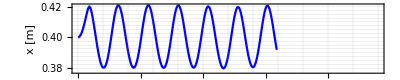
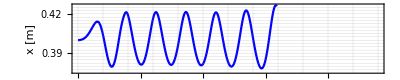
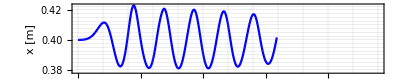
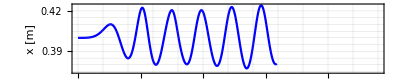

```mathematica
Table[
ListPlot[
{importGetData[name,"simulation_time"],(importGetData[name,data,3])}ᵀ,
Joined->{True,True},
PlotRange->{{0,12},All},
FrameLabel->{(*Style["t [s]",FontSize->16,FontFamily->"Times"]*)None,Style["x [m]",FontSize->16,FontFamily->"Times"]},
Evaluate[opt],
Evaluate[plot2Doption]
],{data,{"gauge0_intersection","gauge1_intersection","gauge2_intersection","gauge3_intersection"}}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],mesh<>"_t_vs_elevation_Ren2015.jpg"}],%[[1]],ImageResolution->150];
```

NotebookDirectory::nosv: ノートブックbwbh6_shmは保存されていません．

Export::chtype: 第1引数FileNameJoin[{$Failed,meshA_t_vs_elevation_Ren2015.jpg}]は有効なファイル指定ではありません．